```mathematica
init=(x-1.5)^2+y^2≤0.25//Rationalize;
unsafe=(x+1)^2+(y+1)^2≤0.16//Rationalize;
Q=-3≤x≤3 && -3≤y≤3;
vf={y,-x+1/3*x^3-y}//Rationalize (* Prajna *)
vf=-{-2(y+1)^2,-(x+1)}//Rationalize


vars={x,y};
```

{y,-x+x^3/3-y}

{2 (1+y)^2,1+x}

```mathematica
problem={init, {vf,vars,Q}, Not[unsafe]} (* Safety verification problem *)
```

{(-3/2+x)^2+y^2≤1/4,{{2 (1+y)^2,1+x},{x,y},-3≤x≤3&&-3≤y≤3},(1+x)^2+(1+y)^2>4/25}

```mathematica
BC=BarrierCertificate`LPBarrier[5,1,problem]
```

{COEFF6-λ10143+λ10159==0,COEFF1-λ10128+λ10164==0,COEFF7-7 λ10128-(7 λ10129)/5-λ10130+(3 λ10149)/5+3 λ10164-(7 λ10165)/5-λ10166+(3 λ10179)/5==0,COEFF2-λ10129+λ10149-λ10165+λ10179==0,COEFF3-λ10131-λ10150+λ10167+λ10180==0,COEFF8-(28 λ10129)/5-(14 λ10131)/5-λ10132+(28 λ10149)/5-(6 λ10150)/5+λ10151-(12 λ10165)/5+(14 λ10167)/5+λ10168+(12 λ10179)/5+(6 λ10180)/5-λ10181==0,COEFF12-(98 λ10128)/5-(196 λ10129)/25-(28 λ10130)/5-(49 λ10131)/25-(7 λ10132)/5-λ10133+(84 λ10149)/25-(9 λ10150)/25+(3 λ10151)/5+(18 λ10164)/5-(84 λ10165)/25-(12 λ10166)/5+(49 λ10167)/25+(7 λ10168)/5+λ10169+(36 λ10179)/25+(9 λ10180)/25-(3 λ10181)/5==0,COEFF4-λ10134+λ10152-λ10170+λ10182==0,COEFF9-(21 λ10131)/5-(21 λ10134)/5-λ10135-(21 λ10150)/5+(9 λ10152)/5-λ10153+(9 λ10167)/5-(21 λ10170)/5-λ10171+(9 λ10180)/5+(9 λ10182)/5-λ10183==0,COEFF16-(686 λ10128)/25-(2058 λ10129)/125-(294 λ10130)/25-(1029 λ10131)/125-(147 λ10132)/25-(21 λ10133)/5-(343 λ10134)/125-(49 λ10135)/25-(7 λ10136)/5-λ10137+(882 λ10149)/125-(189 λ10150)/125+(63 λ10151)/25+(27 λ10152)/125-(9 λ10153)/25+(3 λ10154)/5+(54 λ10164)/25-(378 λ10165)/125-(54 λ10166)/25+(441 λ10167)/125+(63 λ10168)/25+(9 λ10169)/5-(343 λ10170)/125-(49 λ10171)/25-(7 λ10172)/5-λ10173+(162 λ10179)/125+(81 λ10180)/125-(27 λ10181)/25+(27 λ10182)/125-(9 λ10183)/25+(3 λ10184)/5==0,COEFF13-(294 λ10129)/25-(294 λ10131)/25-(21 λ10132)/5-(147 λ10134)/25-(14 λ10135)/5-λ10136+(294 λ10149)/25-(126 λ10150)/25+(21 λ10151)/5+(27 λ10152)/25-(6 λ10153)/5+λ10154-(54 λ10165)/25+(126 λ10167)/25+(9 λ10168)/5-(147 λ10170)/25-(14 λ10171)/5-λ10172+(54 λ10179)/25+(54 λ10180)/25-(9 λ10181)/5+(27 λ10182)/25-(6 λ10183)/5+λ10184==0,COEFF11-(7 λ10138)/5-7 λ10143-λ10144-(7 λ10155)/5+3 λ10159-λ10160+(3 λ10174)/5+(3 λ10185)/5==0,COEFF5-λ10138-λ10155+λ10174+λ10185==0,COEFF10-(14 λ10134)/5-(28 λ10138)/5-λ10139+(14 λ10152)/5-(12 λ10155)/5+λ10156-(6 λ10170)/5+(28 λ10174)/5+λ10175+(6 λ10182)/5+(12 λ10185)/5-λ10186==0,COEFF15-(49 λ10134)/25-(196 λ10138)/25-(7 λ10139)/5-(98 λ10143)/5-(28 λ10144)/5-λ10145+(49 λ10152)/25-(84 λ10155)/25+(7 λ10156)/5+(18 λ10159)/5-(12 λ10160)/5+λ10161-(9 λ10170)/25+(84 λ10174)/25+(3 λ10175)/5+(9 λ10182)/25+(36 λ10185)/25-(3 λ10186)/5==0,COEFF18-(343 λ10131)/125-(1029 λ10134)/125-(49 λ10135)/25-(2058 λ10138)/125-(147 λ10139)/25-(7 λ10140)/5-(686 λ10143)/25-(294 λ10144)/25-(21 λ10145)/5-λ10146-(343 λ10150)/125+(441 λ10152)/125-(49 λ10153)/25-(378 λ10155)/125+(63 λ10156)/25-(7 λ10157)/5+(54 λ10159)/25-(54 λ10160)/25+(9 λ10161)/5-λ10162+(27 λ10167)/125-(189 λ10170)/125-(9 λ10171)/25+(882 λ10174)/125+(63 λ10175)/25+(3 λ10176)/5+(27 λ10180)/125+(81 λ10182)/125-(9 λ10183)/25+(162 λ10185)/125-(27 λ10186)/25+(3 λ10187)/5==0,COEFF14-(147 λ10131)/25-(294 λ10134)/25-(14 λ10135)/5-(294 λ10138)/25-(21 λ10139)/5-λ10140-(147 λ10150)/25+(126 λ10152)/25-(14 λ10153)/5-(54 λ10155)/25+(9 λ10156)/5-λ10157+(27 λ10167)/25-(126 λ10170)/25-(6 λ10171)/5+(294 λ10174)/25+(21 λ10175)/5+λ10176+(27 λ10180)/25+(54 λ10182)/25-(6 λ10183)/5+(54 λ10185)/25-(9 λ10186)/5+λ10187==0,COEFF17-(1372 λ10129)/125-(2058 λ10131)/125-(147 λ10132)/25-(2058 λ10134)/125-(196 λ10135)/25-(14 λ10136)/5-(1372 λ10138)/125-(147 λ10139)/25-(14 λ10140)/5-λ10141+(1372 λ10149)/125-(882 λ10150)/125+(147 λ10151)/25+(378 λ10152)/125-(84 λ10153)/25+(14 λ10154)/5-(108 λ10155)/125+(27 λ10156)/25-(6 λ10157)/5+λ10158-(108 λ10165)/125+(378 λ10167)/125+(27 λ10168)/25-(882 λ10170)/125-(84 λ10171)/25-(6 λ10172)/5+(1372 λ10174)/125+(147 λ10175)/25+(14 λ10176)/5+λ10177+(108 λ10179)/125+(162 λ10180)/125-(27 λ10181)/25+(162 λ10182)/125-(36 λ10183)/25+(6 λ10184)/5+(108 λ10185)/125-(27 λ10186)/25+(6 λ10187)/5-λ10188==0,COEFF19-(2401 λ10128)/125-(9604 λ10129)/625-(1372 λ10130)/125-(7203 λ10131)/625-(1029 λ10132)/125-(147 λ10133)/25-(4802 λ10134)/625-(686 λ10135)/125-(98 λ10136)/25-(14 λ10137)/5-(2401 λ10138)/625-(343 λ10139)/125-(49 λ10140)/25-(7 λ10141)/5-λ10142+(4116 λ10149)/625-(1323 λ10150)/625+(441 λ10151)/125+(378 λ10152)/625-(126 λ10153)/125+(42 λ10154)/25-(81 λ10155)/625+(27 λ10156)/125-(9 λ10157)/25+(3 λ10158)/5+(81 λ10164)/125-(756 λ10165)/625-(108 λ10166)/125+(1323 λ10167)/625+(189 λ10168)/125+(27 λ10169)/25-(2058 λ10170)/625-(294 λ10171)/125-(42 λ10172)/25-(6 λ10173)/5+(2401 λ10174)/625+(343 λ10175)/125+(49 λ10176)/25+(7 λ10177)/5+λ10178+(324 λ10179)/625+(243 λ10180)/625-(81 λ10181)/125+(162 λ10182)/625-(54 λ10183)/125+(18 λ10184)/25+(81 λ10185)/625-(27 λ10186)/125+(9 λ10187)/25-(3 λ10188)/5==0,COEFF20-(2401 λ10129)/625-(4802 λ10131)/625-(343 λ10132)/125-(7203 λ10134)/625-(686 λ10135)/125-(49 λ10136)/25-(9604 λ10138)/625-(1029 λ10139)/125-(98 λ10140)/25-(7 λ10141)/5-(2401 λ10143)/125-(1372 λ10144)/125-(147 λ10145)/25-(14 λ10146)/5-λ10147+(2401 λ10149)/625-(2058 λ10150)/625+(343 λ10151)/125+(1323 λ10152)/625-(294 λ10153)/125+(49 λ10154)/25-(756 λ10155)/625+(189 λ10156)/125-(42 λ10157)/25+(7 λ10158)/5+(81 λ10159)/125-(108 λ10160)/125+(27 λ10161)/25-(6 λ10162)/5+λ10163-(81 λ10165)/625+(378 λ10167)/625+(27 λ10168)/125-(1323 λ10170)/625-(126 λ10171)/125-(9 λ10172)/25+(4116 λ10174)/625+(441 λ10175)/125+(42 λ10176)/25+(3 λ10177)/5+(81 λ10179)/625+(162 λ10180)/625-(27 λ10181)/125+(243 λ10182)/625-(54 λ10183)/125+(9 λ10184)/25+(324 λ10185)/625-(81 λ10186)/125+(18 λ10187)/25-(3 λ10188)/5==0,-1/100+COEFF21-(16807 λ10128)/3125-(16807 λ10129)/3125-(2401 λ10130)/625-(16807 λ10131)/3125-(2401 λ10132)/625-(343 λ10133)/125-(16807 λ10134)/3125-(2401 λ10135)/625-(343 λ10136)/125-(49 λ10137)/25-(16807 λ10138)/3125-(2401 λ10139)/625-(343 λ10140)/125-(49 λ10141)/25-(7 λ10142)/5-(16807 λ10143)/3125-(2401 λ10144)/625-(343 λ10145)/125-(49 λ10146)/25-(7 λ10147)/5-λ10148+(7203 λ10149)/3125-(3087 λ10150)/3125+(1029 λ10151)/625+(1323 λ10152)/3125-(441 λ10153)/625+(147 λ10154)/125-(567 λ10155)/3125+(189 λ10156)/625-(63 λ10157)/125+(21 λ10158)/25+(243 λ10159)/3125-(81 λ10160)/625+(27 λ10161)/125-(9 λ10162)/25+(3 λ10163)/5+(243 λ10164)/3125-(567 λ10165)/3125-(81 λ10166)/625+(1323 λ10167)/3125+(189 λ10168)/625+(27 λ10169)/125-(3087 λ10170)/3125-(441 λ10171)/625-(63 λ10172)/125-(9 λ10173)/25+(7203 λ10174)/3125+(1029 λ10175)/625+(147 λ10176)/125+(21 λ10177)/25+(3 λ10178)/5+(243 λ10179)/3125+(243 λ10180)/3125-(81 λ10181)/625+(243 λ10182)/3125-(81 λ10183)/625+(27 λ10184)/125+(243 λ10185)/3125-(81 λ10186)/625+(27 λ10187)/125-(9 λ10188)/25==0,-COEFF6-λ10204+λ10220==0,-COEFF1-λ10189+λ10225==0,-COEFF7+5 λ10189-λ10190/2-λ10191-λ10210/2-10 λ10225-λ10226/2-λ10227-λ10240/2==0,-COEFF2-λ10190+λ10210-λ10226+λ10240==0,-COEFF3-λ10192-λ10211+λ10228+λ10241==0,-COEFF8+4 λ10190-λ10192-λ10193-4 λ10210+λ10211+λ10212+8 λ10226+λ10228+λ10229-8 λ10240-λ10241-λ10242==0,-COEFF12-10 λ10189+2 λ10190+4 λ10191-λ10192/4-λ10193/2-λ10194+2 λ10210-λ10211/4-λ10212/2+40 λ10225+4 λ10226+8 λ10227+λ10228/4+λ10229/2+λ10230+4 λ10240+λ10241/4+λ10242/2==0,-COEFF4-λ10195+λ10213-λ10231+λ10243==0,-COEFF9+3 λ10192-(3 λ10195)/2-λ10196+3 λ10211-(3 λ10213)/2-λ10214-6 λ10228-(3 λ10231)/2-λ10232-6 λ10241-(3 λ10243)/2-λ10244==0,-COEFF16+10 λ10189-3 λ10190-6 λ10191+(3 λ10192)/4+(3 λ10193)/2+3 λ10194-λ10195/8-λ10196/4-λ10197/2-λ10198-3 λ10210+(3 λ10211)/4+(3 λ10212)/2-λ10213/8-λ10214/4-λ10215/2-80 λ10225-12 λ10226-24 λ10227-(3 λ10228)/2-3 λ10229-6 λ10230-λ10231/8-λ10232/4-λ10233/2-λ10234-12 λ10240-(3 λ10241)/2-3 λ10242-λ10243/8-λ10244/4-λ10245/2==0,-COEFF13-6 λ10190+3 λ10192+3 λ10193-(3 λ10195)/4-λ10196-λ10197+6 λ10210-3 λ10211-3 λ10212+(3 λ10213)/4+λ10214+λ10215-24 λ10226-6 λ10228-6 λ10229-(3 λ10231)/4-λ10232-λ10233+24 λ10240+6 λ10241+6 λ10242+(3 λ10243)/4+λ10244+λ10245==0,-COEFF11+λ10199-(5 λ10204)/2-λ10205+λ10216-(5 λ10220)/2-λ10221-2 λ10235-2 λ10246==0,-COEFF5-λ10199-λ10216+λ10235+λ10246==0,-COEFF10+2 λ10195-2 λ10199-λ10200-2 λ10213+2 λ10216+λ10217+4 λ10231+2 λ10235+λ10236-4 λ10243-2 λ10246-λ10247==0,-COEFF15-λ10195+2 λ10199+λ10200-(5 λ10204)/2-2 λ10205-λ10206+λ10213-2 λ10216-λ10217+(5 λ10220)/2+2 λ10221+λ10222-4 λ10231-4 λ10235-2 λ10236+4 λ10243+4 λ10246+2 λ10247==0,-COEFF18+λ10192-(3 λ10195)/2-λ10196+(3 λ10199)/2+(3 λ10200)/2+λ10201-(5 λ10204)/4-(3 λ10205)/2-(3 λ10206)/2-λ10207+λ10211-(3 λ10213)/2-λ10214+(3 λ10216)/2+(3 λ10217)/2+λ10218-(5 λ10220)/4-(3 λ10221)/2-(3 λ10222)/2-λ10223-8 λ10228-6 λ10231-4 λ10232-3 λ10235-3 λ10236-2 λ10237-8 λ10241-6 λ10243-4 λ10244-3 λ10246-3 λ10247-2 λ10248==0,-COEFF14-3 λ10192+3 λ10195+2 λ10196-(3 λ10199)/2-(3 λ10200)/2-λ10201-3 λ10211+3 λ10213+2 λ10214-(3 λ10216)/2-(3 λ10217)/2-λ10218+12 λ10228+6 λ10231+4 λ10232+(3 λ10235)/2+(3 λ10236)/2+λ10237+12 λ10241+6 λ10243+4 λ10244+(3 λ10246)/2+(3 λ10247)/2+λ10248==0,-COEFF17+4 λ10190-3 λ10192-3 λ10193+(3 λ10195)/2+2 λ10196+2 λ10197-λ10199/2-(3 λ10200)/4-λ10201-λ10202-4 λ10210+3 λ10211+3 λ10212-(3 λ10213)/2-2 λ10214-2 λ10215+λ10216/2+(3 λ10217)/4+λ10218+λ10219+32 λ10226+12 λ10228+12 λ10229+3 λ10231+4 λ10232+4 λ10233+λ10235/2+(3 λ10236)/4+λ10237+λ10238-32 λ10240-12 λ10241-12 λ10242-3 λ10243-4 λ10244-4 λ10245-λ10246/2-(3 λ10247)/4-λ10248-λ10249==0,-COEFF21+λ10189-λ10190/2-λ10191+λ10192/4+λ10193/2+λ10194-λ10195/8-λ10196/4-λ10197/2-λ10198+λ10199/16+λ10200/8+λ10201/4+λ10202/2+λ10203-λ10204/32-λ10205/16-λ10206/8-λ10207/4-λ10208/2-λ10209-λ10210/2+λ10211/4+λ10212/2-λ10213/8-λ10214/4-λ10215/2+λ10216/16+λ10217/8+λ10218/4+λ10219/2-λ10220/32-λ10221/16-λ10222/8-λ10223/4-λ10224/2-32 λ10225-8 λ10226-16 λ10227-2 λ10228-4 λ10229-8 λ10230-λ10231/2-λ10232-2 λ10233-4 λ10234-λ10235/8-λ10236/4-λ10237/2-λ10238-2 λ10239-8 λ10240-2 λ10241-4 λ10242-λ10243/2-λ10244-2 λ10245-λ10246/8-λ10247/4-λ10248/2-λ10249==0,-COEFF19-5 λ10189+2 λ10190+4 λ10191-(3 λ10192)/4-(3 λ10193)/2-3 λ10194+λ10195/4+λ10196/2+λ10197+2 λ10198-λ10199/16-λ10200/8-λ10201/4-λ10202/2-λ10203+2 λ10210-(3 λ10211)/4-(3 λ10212)/2+λ10213/4+λ10214/2+λ10215-λ10216/16-λ10217/8-λ10218/4-λ10219/2+80 λ10225+16 λ10226+32 λ10227+3 λ10228+6 λ10229+12 λ10230+λ10231/2+λ10232+2 λ10233+4 λ10234+λ10235/16+λ10236/8+λ10237/4+λ10238/2+λ10239+16 λ10240+3 λ10241+6 λ10242+λ10243/2+λ10244+2 λ10245+λ10246/16+λ10247/8+λ10248/4+λ10249/2==0,-COEFF20-λ10190+λ10192+λ10193-(3 λ10195)/4-λ10196-λ10197+λ10199/2+(3 λ10200)/4+λ10201+λ10202-(5 λ10204)/16-λ10205/2-(3 λ10206)/4-λ10207-λ10208+λ10210-λ10211-λ10212+(3 λ10213)/4+λ10214+λ10215-λ10216/2-(3 λ10217)/4-λ10218-λ10219+(5 λ10220)/16+λ10221/2+(3 λ10222)/4+λ10223+λ10224-16 λ10226-8 λ10228-8 λ10229-3 λ10231-4 λ10232-4 λ10233-λ10235-(3 λ10236)/2-2 λ10237-2 λ10238+16 λ10240+8 λ10241+8 λ10242+3 λ10243+4 λ10244+4 λ10245+λ10246+(3 λ10247)/2+2 λ10248+2 λ10249==0,-2 COEFF5-λ10271-λ10293==0,-λ10250-λ10299==0,-λ10251+λ10278+λ10300-λ10320==0,COEFF1-COEFF2-18 λ10250-3 λ10251-λ10252-3 λ10278+18 λ10299+3 λ10300+λ10301+3 λ10320==0,-10 COEFF1-λ10253-λ10279-λ10302-λ10321==0,-10 COEFF1-COEFF2+COEFF7-COEFF8-135 λ10250-45 λ10251-15 λ10252-9 λ10253-3 λ10254-λ10255-45 λ10278-9 λ10279-3 λ10280-135 λ10299-45 λ10300-15 λ10301-9 λ10302-3 λ10303-λ10304-45 λ10320-9 λ10321-3 λ10322==0,-20 COEFF1+COEFF2-2 COEFF3-15 λ10251-6 λ10253-λ10254+15 λ10278+6 λ10279+λ10280-15 λ10300-6 λ10302-λ10303+15 λ10320+6 λ10321+λ10322==0,-8 COEFF2-λ10256+λ10281+λ10305-λ10323==0,-16 COEFF2+COEFF3-3 COEFF4-8 COEFF7-12 λ10253-9 λ10256-λ10257-12 λ10279-9 λ10281-λ10282+12 λ10302+9 λ10305+λ10306+12 λ10321+9 λ10323+λ10324==0,-8 COEFF2-2 COEFF3-16 COEFF7+COEFF8-2 COEFF9-90 λ10251-72 λ10253-12 λ10254-27 λ10256-6 λ10257-λ10258+90 λ10278+72 λ10279+12 λ10280+27 λ10281+6 λ10282+λ10283+90 λ10300+72 λ10302+12 λ10303+27 λ10305+6 λ10306+λ10307-90 λ10320-72 λ10321-12 λ10322-27 λ10323-6 λ10324-λ10325==0,COEFF12-COEFF13-8 COEFF7-COEFF8-540 λ10250-270 λ10251-90 λ10252-108 λ10253-36 λ10254-12 λ10255-27 λ10256-9 λ10257-3 λ10258-λ10259-270 λ10278-108 λ10279-36 λ10280-27 λ10281-9 λ10282-3 λ10283+540 λ10299+270 λ10300+90 λ10301+108 λ10302+36 λ10303+12 λ10304+27 λ10305+9 λ10306+3 λ10307+λ10308+270 λ10320+108 λ10321+36 λ10322+27 λ10323+9 λ10324+3 λ10325==0,-6 COEFF3-λ10260-λ10284-λ10309-λ10326==0,-12 COEFF3+COEFF4-4 COEFF5-6 COEFF8-9 λ10256-12 λ10260-λ10261+9 λ10281+12 λ10284+λ10285-9 λ10305-12 λ10309-λ10310+9 λ10323+12 λ10326+λ10327==0,-3 COEFF10-6 COEFF12-6 COEFF3-3 COEFF4-12 COEFF8+COEFF9-54 λ10253-81 λ10256-9 λ10257-54 λ10260-9 λ10261-λ10262-54 λ10279-81 λ10281-9 λ10282-54 λ10284-9 λ10285-λ10286-54 λ10302-81 λ10305-9 λ10306-54 λ10309-9 λ10310-λ10311-54 λ10321-81 λ10323-9 λ10324-54 λ10326-9 λ10327-λ10328==0,-6 COEFF12-COEFF13+COEFF16-COEFF17-1215 λ10250-810 λ10251-270 λ10252-486 λ10253-162 λ10254-54 λ10255-243 λ10256-81 λ10257-27 λ10258-9 λ10259-81 λ10260-27 λ10261-9 λ10262-3 λ10263-λ10264-810 λ10278-486 λ10279-162 λ10280-243 λ10281-81 λ10282-27 λ10283-81 λ10284-27 λ10285-9 λ10286-3 λ10287-1215 λ10299-810 λ10300-270 λ10301-486 λ10302-162 λ10303-54 λ10304-243 λ10305-81 λ10306-27 λ10307-9 λ10308-81 λ10309-27 λ10310-9 λ10311-3 λ10312-λ10313-810 λ10320-486 λ10321-162 λ10322-243 λ10323-81 λ10324-27 λ10325-81 λ10326-27 λ10327-9 λ10328-3 λ10329==0,-12 COEFF12+COEFF13-2 COEFF14-6 COEFF8-2 COEFF9-270 λ10251-324 λ10253-54 λ10254-243 λ10256-54 λ10257-9 λ10258-108 λ10260-27 λ10261-6 λ10262-λ10263+270 λ10278+324 λ10279+54 λ10280+243 λ10281+54 λ10282+9 λ10283+108 λ10284+27 λ10285+6 λ10286+λ10287-270 λ10300-324 λ10302-54 λ10303-243 λ10305-54 λ10306-9 λ10307-108 λ10309-27 λ10310-6 λ10311-λ10312+270 λ10320+324 λ10321+54 λ10322+243 λ10323+54 λ10324+9 λ10325+108 λ10326+27 λ10327+6 λ10328+λ10329==0,-4 COEFF4-λ10265+λ10288+λ10314-λ10330==0,-2 COEFF10-4 COEFF5+COEFF6-3 λ10265-18 λ10271-λ10272+3 λ10288+18 λ10293+λ10294-3 λ10314+3 λ10330==0,-4 COEFF10+COEFF11-2 COEFF14-2 COEFF5-5 COEFF6-9 λ10260-45 λ10265-3 λ10266-135 λ10271-15 λ10272-λ10273-9 λ10284-45 λ10288-3 λ10289-135 λ10293-15 λ10294-λ10295-9 λ10309-45 λ10314-3 λ10315-9 λ10326-45 λ10330-3 λ10331==0,-8 COEFF4+COEFF5-5 COEFF6-4 COEFF9-6 λ10260-15 λ10265-λ10266-6 λ10284-15 λ10288-λ10289+6 λ10309+15 λ10314+λ10315+6 λ10326+15 λ10330+λ10331==0,COEFF10-4 COEFF11-4 COEFF13-4 COEFF4-4 COEFF5-8 COEFF9-27 λ10256-72 λ10260-6 λ10261-90 λ10265-12 λ10266-λ10267+27 λ10281+72 λ10284+6 λ10285+90 λ10288+12 λ10289+λ10290+27 λ10305+72 λ10309+6 λ10310+90 λ10314+12 λ10315+λ10316-27 λ10323-72 λ10326-6 λ10327-90 λ10330-12 λ10331-λ10332==0,-2 COEFF10-4 COEFF11-4 COEFF14+COEFF15-2 COEFF17-27 λ10256-108 λ10260-9 λ10261-270 λ10265-36 λ10266-3 λ10267-540 λ10271-90 λ10272-12 λ10273-λ10274+27 λ10281+108 λ10284+9 λ10285+270 λ10288+36 λ10289+3 λ10290+540 λ10293+90 λ10294+12 λ10295+λ10296-27 λ10305-108 λ10309-9 λ10310-270 λ10314-36 λ10315-3 λ10316+27 λ10323+108 λ10326+9 λ10327+270 λ10330+36 λ10331+3 λ10332==0,-2 COEFF14-3 COEFF15-4 COEFF17+COEFF18-2 COEFF19-81 λ10253-243 λ10256-27 λ10257-486 λ10260-81 λ10261-9 λ10262-810 λ10265-162 λ10266-27 λ10267-3 λ10268-1215 λ10271-270 λ10272-54 λ10273-9 λ10274-λ10275-81 λ10279-243 λ10281-27 λ10282-486 λ10284-81 λ10285-9 λ10286-810 λ10288-162 λ10289-27 λ10290-3 λ10291-1215 λ10293-270 λ10294-54 λ10295-9 λ10296-λ10297-81 λ10302-243 λ10305-27 λ10306-486 λ10309-81 λ10310-9 λ10311-810 λ10314-162 λ10315-27 λ10316-3 λ10317-81 λ10321-243 λ10323-27 λ10324-486 λ10326-81 λ10327-9 λ10328-810 λ10330-162 λ10331-27 λ10332-3 λ10333==0,-3 COEFF10-8 COEFF13+COEFF14-3 COEFF15-4 COEFF16-4 COEFF9-108 λ10253-243 λ10256-27 λ10257-324 λ10260-54 λ10261-6 λ10262-270 λ10265-54 λ10266-9 λ10267-λ10268-108 λ10279-243 λ10281-27 λ10282-324 λ10284-54 λ10285-6 λ10286-270 λ10288-54 λ10289-9 λ10290-λ10291+108 λ10302+243 λ10305+27 λ10306+324 λ10309+54 λ10310+6 λ10311+270 λ10314+54 λ10315+9 λ10316+λ10317+108 λ10321+243 λ10323+27 λ10324+324 λ10326+54 λ10327+6 λ10328+270 λ10330+54 λ10331+9 λ10332+λ10333==0,-2 COEFF19-COEFF20+COEFF21-729 λ10250-729 λ10251-243 λ10252-729 λ10253-243 λ10254-81 λ10255-729 λ10256-243 λ10257-81 λ10258-27 λ10259-729 λ10260-243 λ10261-81 λ10262-27 λ10263-9 λ10264-729 λ10265-243 λ10266-81 λ10267-27 λ10268-9 λ10269-3 λ10270-729 λ10271-243 λ10272-81 λ10273-27 λ10274-9 λ10275-3 λ10276-λ10277-729 λ10278-729 λ10279-243 λ10280-729 λ10281-243 λ10282-81 λ10283-729 λ10284-243 λ10285-81 λ10286-27 λ10287-729 λ10288-243 λ10289-81 λ10290-27 λ10291-9 λ10292-729 λ10293-243 λ10294-81 λ10295-27 λ10296-9 λ10297-3 λ10298-729 λ10299-729 λ10300-243 λ10301-729 λ10302-243 λ10303-81 λ10304-729 λ10305-243 λ10306-81 λ10307-27 λ10308-729 λ10309-243 λ10310-81 λ10311-27 λ10312-9 λ10313-729 λ10314-243 λ10315-81 λ10316-27 λ10317-9 λ10318-3 λ10319-729 λ10320-729 λ10321-243 λ10322-729 λ10323-243 λ10324-81 λ10325-729 λ10326-243 λ10327-81 λ10328-27 λ10329-729 λ10330-243 λ10331-81 λ10332-27 λ10333-9 λ10334==0,-4 COEFF13-2 COEFF14-8 COEFF16+COEFF17-2 COEFF18-405 λ10251-648 λ10253-108 λ10254-729 λ10256-162 λ10257-27 λ10258-648 λ10260-162 λ10261-36 λ10262-6 λ10263-405 λ10265-108 λ10266-27 λ10267-6 λ10268-λ10269+405 λ10278+648 λ10279+108 λ10280+729 λ10281+162 λ10282+27 λ10283+648 λ10284+162 λ10285+36 λ10286+6 λ10287+405 λ10288+108 λ10289+27 λ10290+6 λ10291+λ10292+405 λ10300+648 λ10302+108 λ10303+729 λ10305+162 λ10306+27 λ10307+648 λ10309+162 λ10310+36 λ10311+6 λ10312+405 λ10314+108 λ10315+27 λ10316+6 λ10317+λ10318-405 λ10320-648 λ10321-108 λ10322-729 λ10323-162 λ10324-27 λ10325-648 λ10326-162 λ10327-36 λ10328-6 λ10329-405 λ10330-108 λ10331-27 λ10332-6 λ10333-λ10334==0,-4 COEFF16-COEFF17+COEFF19-COEFF20-1458 λ10250-1215 λ10251-405 λ10252-972 λ10253-324 λ10254-108 λ10255-729 λ10256-243 λ10257-81 λ10258-27 λ10259-486 λ10260-162 λ10261-54 λ10262-18 λ10263-6 λ10264-243 λ10265-81 λ10266-27 λ10267-9 λ10268-3 λ10269-λ10270-1215 λ10278-972 λ10279-324 λ10280-729 λ10281-243 λ10282-81 λ10283-486 λ10284-162 λ10285-54 λ10286-18 λ10287-243 λ10288-81 λ10289-27 λ10290-9 λ10291-3 λ10292+1458 λ10299+1215 λ10300+405 λ10301+972 λ10302+324 λ10303+108 λ10304+729 λ10305+243 λ10306+81 λ10307+27 λ10308+486 λ10309+162 λ10310+54 λ10311+18 λ10312+6 λ10313+243 λ10314+81 λ10315+27 λ10316+9 λ10317+3 λ10318+λ10319+1215 λ10320+972 λ10321+324 λ10322+729 λ10323+243 λ10324+81 λ10325+486 λ10326+162 λ10327+54 λ10328+18 λ10329+243 λ10330+81 λ10331+27 λ10332+9 λ10333+3 λ10334==0,-2 COEFF17-2 COEFF18-4 COEFF19+COEFF20-243 λ10251-486 λ10253-81 λ10254-729 λ10256-162 λ10257-27 λ10258-972 λ10260-243 λ10261-54 λ10262-9 λ10263-1215 λ10265-324 λ10266-81 λ10267-18 λ10268-3 λ10269-1458 λ10271-405 λ10272-108 λ10273-27 λ10274-6 λ10275-λ10276+243 λ10278+486 λ10279+81 λ10280+729 λ10281+162 λ10282+27 λ10283+972 λ10284+243 λ10285+54 λ10286+9 λ10287+1215 λ10288+324 λ10289+81 λ10290+18 λ10291+3 λ10292+1458 λ10293+405 λ10294+108 λ10295+27 λ10296+6 λ10297+λ10298-243 λ10300-486 λ10302-81 λ10303-729 λ10305-162 λ10306-27 λ10307-972 λ10309-243 λ10310-54 λ10311-9 λ10312-1215 λ10314-324 λ10315-81 λ10316-18 λ10317-3 λ10318+243 λ10320+486 λ10321+81 λ10322+729 λ10323+162 λ10324+27 λ10325+972 λ10326+243 λ10327+54 λ10328+9 λ10329+1215 λ10330+324 λ10331+81 λ10332+18 λ10333+3 λ10334==0,λ10128≥0,λ10129≥0,λ10130≥0,λ10131≥0,λ10132≥0,λ10133≥0,λ10134≥0,λ10135≥0,λ10136≥0,λ10137≥0,λ10138≥0,λ10139≥0,λ10140≥0,λ10141≥0,λ10142≥0,λ10143≥0,λ10144≥0,λ10145≥0,λ10146≥0,λ10147≥0,λ10148≥0,λ10149≥0,λ10150≥0,λ10151≥0,λ10152≥0,λ10153≥0,λ10154≥0,λ10155≥0,λ10156≥0,λ10157≥0,λ10158≥0,λ10159≥0,λ10160≥0,λ10161≥0,λ10162≥0,λ10163≥0,λ10164≥0,λ10165≥0,λ10166≥0,λ10167≥0,λ10168≥0,λ10169≥0,λ10170≥0,λ10171≥0,λ10172≥0,λ10173≥0,λ10174≥0,λ10175≥0,λ10176≥0,λ10177≥0,λ10178≥0,λ10179≥0,λ10180≥0,λ10181≥0,λ10182≥0,λ10183≥0,λ10184≥0,λ10185≥0,λ10186≥0,λ10187≥0,λ10188≥0,λ10189≥0,λ10190≥0,λ10191≥0,λ10192≥0,λ10193≥0,λ10194≥0,λ10195≥0,λ10196≥0,λ10197≥0,λ10198≥0,λ10199≥0,λ10200≥0,λ10201≥0,λ10202≥0,λ10203≥0,λ10204≥0,λ10205≥0,λ10206≥0,λ10207≥0,λ10208≥0,λ10209≥0,λ10210≥0,λ10211≥0,λ10212≥0,λ10213≥0,λ10214≥0,λ10215≥0,λ10216≥0,λ10217≥0,λ10218≥0,λ10219≥0,λ10220≥0,λ10221≥0,λ10222≥0,λ10223≥0,λ10224≥0,λ10225≥0,λ10226≥0,λ10227≥0,λ10228≥0,λ10229≥0,λ10230≥0,λ10231≥0,λ10232≥0,λ10233≥0,λ10234≥0,λ10235≥0,λ10236≥0,λ10237≥0,λ10238≥0,λ10239≥0,λ10240≥0,λ10241≥0,λ10242≥0,λ10243≥0,λ10244≥0,λ10245≥0,λ10246≥0,λ10247≥0,λ10248≥0,λ10249≥0,λ10250≥0,λ10251≥0,λ10252≥0,λ10253≥0,λ10254≥0,λ10255≥0,λ10256≥0,λ10257≥0,λ10258≥0,λ10259≥0,λ10260≥0,λ10261≥0,λ10262≥0,λ10263≥0,λ10264≥0,λ10265≥0,λ10266≥0,λ10267≥0,λ10268≥0,λ10269≥0,λ10270≥0,λ10271≥0,λ10272≥0,λ10273≥0,λ10274≥0,λ10275≥0,λ10276≥0,λ10277≥0,λ10278≥0,λ10279≥0,λ10280≥0,λ10281≥0,λ10282≥0,λ10283≥0,λ10284≥0,λ10285≥0,λ10286≥0,λ10287≥0,λ10288≥0,λ10289≥0,λ10290≥0,λ10291≥0,λ10292≥0,λ10293≥0,λ10294≥0,λ10295≥0,λ10296≥0,λ10297≥0,λ10298≥0,λ10299≥0,λ10300≥0,λ10301≥0,λ10302≥0,λ10303≥0,λ10304≥0,λ10305≥0,λ10306≥0,λ10307≥0,λ10308≥0,λ10309≥0,λ10310≥0,λ10311≥0,λ10312≥0,λ10313≥0,λ10314≥0,λ10315≥0,λ10316≥0,λ10317≥0,λ10318≥0,λ10319≥0,λ10320≥0,λ10321≥0,λ10322≥0,λ10323≥0,λ10324≥0,λ10325≥0,λ10326≥0,λ10327≥0,λ10328≥0,λ10329≥0,λ10330≥0,λ10331≥0,λ10332≥0,λ10333≥0,λ10334≥0}

```mathematica
SMTLIB[a_Times]:="(* "<>StringRiffle[SMTLIB/@List@@a]<>")"
SMTLIB[a_Plus]:="(+ "<>StringRiffle[SMTLIB/@List@@a]<>")"
SMTLIB[a_Power]:="(* "<>StringRiffle[SMTLIB/@Table[(List@@a)[[1]],(List@@a)[[2]]]]<>")"
SMTLIB[a_Rational]:="(/ "<>StringRiffle[SMTLIB/@{Numerator[a],Denominator[a]}]<>")"
SMTLIB[a_Equal]:="(assert (= "<>StringRiffle[SMTLIB/@List@@a]<>"))"
SMTLIB[a_GreaterEqual]:="(assert (>= "<>StringRiffle[SMTLIB/@List@@a]<>"))"
SMTLIB[a_LessEqual]:="(assert (<= "<>StringRiffle[SMTLIB/@List@@a]<>"))"
SMTLIB[a_Less]:="(assert (< "<>StringRiffle[SMTLIB/@List@@a]<>"))"
SMTLIB[a_Greater]:="(assert (> "<>StringRiffle[SMTLIB/@List@@a]<>"))"
SMTLIB[a_List]:=StringRiffle[SMTLIB/@a, "\n"]
SMTLIB[a_]:=StringReplace[ToString[a],"λ"->"LAMBDA"]

SMTLIBvars[vars_List]:=StringRiffle[Map["(declare-fun "<>StringReplace[ToString[#],"λ"->"LAMBDA"]<>" () Real)"&, vars], "\n"]
SMTLIBlogic[logic_String]:="(set-logic "<>logic<>")"
SMTLIBgetvalue[vars_List]:="(get-value ("<>StringRiffle[SMTLIB/@vars]<>"))"
```

```mathematica
lpvars=(Variables/@(First/@BC))//Flatten//DeleteDuplicates//Sort
```

{COEFF1,COEFF10,COEFF11,COEFF12,COEFF13,COEFF14,COEFF15,COEFF16,COEFF17,COEFF18,COEFF19,COEFF2,COEFF20,COEFF21,COEFF3,COEFF4,COEFF5,COEFF6,COEFF7,COEFF8,COEFF9,λ10128,λ10129,λ10130,λ10131,λ10132,λ10133,λ10134,λ10135,λ10136,λ10137,λ10138,λ10139,λ10140,λ10141,λ10142,λ10143,λ10144,λ10145,λ10146,λ10147,λ10148,λ10149,λ10150,λ10151,λ10152,λ10153,λ10154,λ10155,λ10156,λ10157,λ10158,λ10159,λ10160,λ10161,λ10162,λ10163,λ10164,λ10165,λ10166,λ10167,λ10168,λ10169,λ10170,λ10171,λ10172,λ10173,λ10174,λ10175,λ10176,λ10177,λ10178,λ10179,λ10180,λ10181,λ10182,λ10183,λ10184,λ10185,λ10186,λ10187,λ10188,λ10189,λ10190,λ10191,λ10192,λ10193,λ10194,λ10195,λ10196,λ10197,λ10198,λ10199,λ10200,λ10201,λ10202,λ10203,λ10204,λ10205,λ10206,λ10207,λ10208,λ10209,λ10210,λ10211,λ10212,λ10213,λ10214,λ10215,λ10216,λ10217,λ10218,λ10219,λ10220,λ10221,λ10222,λ10223,λ10224,λ10225,λ10226,λ10227,λ10228,λ10229,λ10230,λ10231,λ10232,λ10233,λ10234,λ10235,λ10236,λ10237,λ10238,λ10239,λ10240,λ10241,λ10242,λ10243,λ10244,λ10245,λ10246,λ10247,λ10248,λ10249,λ10250,λ10251,λ10252,λ10253,λ10254,λ10255,λ10256,λ10257,λ10258,λ10259,λ10260,λ10261,λ10262,λ10263,λ10264,λ10265,λ10266,λ10267,λ10268,λ10269,λ10270,λ10271,λ10272,λ10273,λ10274,λ10275,λ10276,λ10277,λ10278,λ10279,λ10280,λ10281,λ10282,λ10283,λ10284,λ10285,λ10286,λ10287,λ10288,λ10289,λ10290,λ10291,λ10292,λ10293,λ10294,λ10295,λ10296,λ10297,λ10298,λ10299,λ10300,λ10301,λ10302,λ10303,λ10304,λ10305,λ10306,λ10307,λ10308,λ10309,λ10310,λ10311,λ10312,λ10313,λ10314,λ10315,λ10316,λ10317,λ10318,λ10319,λ10320,λ10321,λ10322,λ10323,λ10324,λ10325,λ10326,λ10327,λ10328,λ10329,λ10330,λ10331,λ10332,λ10333,λ10334}

(set-logic QF_LRA)

```mathematica
"(set-option:print-success true)"<>"\n"<>
"(set-option:produce-models true)"<>"\n"<>
SMTLIBlogic["QF_LRA"]<>"\n"<>
SMTLIBvars[lpvars]<>"\n"<>
SMTLIB[ BC]<>"\n"<>
"(check-sat)"<>"\n"<>
SMTLIBgetvalue[lpvars]<>"\n"<>
"(get-model)"<>"\n"<>
"(exit)"
```

(set-option:print-success true)
(set-option:produce-models true)
(set-logic QF_LRA)
(declare-fun COEFF1 () Real)
(declare-fun COEFF10 () Real)
(declare-fun COEFF11 () Real)
(declare-fun COEFF12 () Real)
(declare-fun COEFF13 () Real)
(declare-fun COEFF14 () Real)
(declare-fun COEFF15 () Real)
(declare-fun COEFF16 () Real)
(declare-fun COEFF17 () Real)
(declare-fun COEFF18 () Real)
(declare-fun COEFF19 () Real)
(declare-fun COEFF2 () Real)
(declare-fun COEFF20 () Real)
(declare-fun COEFF21 () Real)
(declare-fun COEFF3 () Real)
(declare-fun COEFF4 () Real)
(declare-fun COEFF5 () Real)
(declare-fun COEFF6 () Real)
(declare-fun COEFF7 () Real)
(declare-fun COEFF8 () Real)
(declare-fun COEFF9 () Real)
(declare-fun LAMBDA10128 () Real)
(declare-fun LAMBDA10129 () Real)
(declare-fun LAMBDA10130 () Real)
(declare-fun LAMBDA10131 () Real)
(declare-fun LAMBDA10132 () Real)
(declare-fun LAMBDA10133 () Real)
(declare-fun LAMBDA10134 () Real)
(declare-fun LAMBDA10135 () Real)
(declare-fun LAMBDA10136 () Real)
(declare-fun LAMBDA10137 () Real)
(declare-fun LAMBDA10138 () Real)
(declare-fun LAMBDA10139 () Real)
(declare-fun LAMBDA10140 () Real)
(declare-fun LAMBDA10141 () Real)
(declare-fun LAMBDA10142 () Real)
(declare-fun LAMBDA10143 () Real)
(declare-fun LAMBDA10144 () Real)
(declare-fun LAMBDA10145 () Real)
(declare-fun LAMBDA10146 () Real)
(declare-fun LAMBDA10147 () Real)
(declare-fun LAMBDA10148 () Real)
(declare-fun LAMBDA10149 () Real)
(declare-fun LAMBDA10150 () Real)
(declare-fun LAMBDA10151 () Real)
(declare-fun LAMBDA10152 () Real)
(declare-fun LAMBDA10153 () Real)
(declare-fun LAMBDA10154 () Real)
(declare-fun LAMBDA10155 () Real)
(declare-fun LAMBDA10156 () Real)
(declare-fun LAMBDA10157 () Real)
(declare-fun LAMBDA10158 () Real)
(declare-fun LAMBDA10159 () Real)
(declare-fun LAMBDA10160 () Real)
(declare-fun LAMBDA10161 () Real)
(declare-fun LAMBDA10162 () Real)
(declare-fun LAMBDA10163 () Real)
(declare-fun LAMBDA10164 () Real)
(declare-fun LAMBDA10165 () Real)
(declare-fun LAMBDA10166 () Real)
(declare-fun LAMBDA10167 () Real)
(declare-fun LAMBDA10168 () Real)
(declare-fun LAMBDA10169 () Real)
(declare-fun LAMBDA10170 () Real)
(declare-fun LAMBDA10171 () Real)
(declare-fun LAMBDA10172 () Real)
(declare-fun LAMBDA10173 () Real)
(declare-fun LAMBDA10174 () Real)
(declare-fun LAMBDA10175 () Real)
(declare-fun LAMBDA10176 () Real)
(declare-fun LAMBDA10177 () Real)
(declare-fun LAMBDA10178 () Real)
(declare-fun LAMBDA10179 () Real)
(declare-fun LAMBDA10180 () Real)
(declare-fun LAMBDA10181 () Real)
(declare-fun LAMBDA10182 () Real)
(declare-fun LAMBDA10183 () Real)
(declare-fun LAMBDA10184 () Real)
(declare-fun LAMBDA10185 () Real)
(declare-fun LAMBDA10186 () Real)
(declare-fun LAMBDA10187 () Real)
(declare-fun LAMBDA10188 () Real)
(declare-fun LAMBDA10189 () Real)
(declare-fun LAMBDA10190 () Real)
(declare-fun LAMBDA10191 () Real)
(declare-fun LAMBDA10192 () Real)
(declare-fun LAMBDA10193 () Real)
(declare-fun LAMBDA10194 () Real)
(declare-fun LAMBDA10195 () Real)
(declare-fun LAMBDA10196 () Real)
(declare-fun LAMBDA10197 () Real)
(declare-fun LAMBDA10198 () Real)
(declare-fun LAMBDA10199 () Real)
(declare-fun LAMBDA10200 () Real)
(declare-fun LAMBDA10201 () Real)
(declare-fun LAMBDA10202 () Real)
(declare-fun LAMBDA10203 () Real)
(declare-fun LAMBDA10204 () Real)
(declare-fun LAMBDA10205 () Real)
(declare-fun LAMBDA10206 () Real)
(declare-fun LAMBDA10207 () Real)
(declare-fun LAMBDA10208 () Real)
(declare-fun LAMBDA10209 () Real)
(declare-fun LAMBDA10210 () Real)
(declare-fun LAMBDA10211 () Real)
(declare-fun LAMBDA10212 () Real)
(declare-fun LAMBDA10213 () Real)
(declare-fun LAMBDA10214 () Real)
(declare-fun LAMBDA10215 () Real)
(declare-fun LAMBDA10216 () Real)
(declare-fun LAMBDA10217 () Real)
(declare-fun LAMBDA10218 () Real)
(declare-fun LAMBDA10219 () Real)
(declare-fun LAMBDA10220 () Real)
(declare-fun LAMBDA10221 () Real)
(declare-fun LAMBDA10222 () Real)
(declare-fun LAMBDA10223 () Real)
(declare-fun LAMBDA10224 () Real)
(declare-fun LAMBDA10225 () Real)
(declare-fun LAMBDA10226 () Real)
(declare-fun LAMBDA10227 () Real)
(declare-fun LAMBDA10228 () Real)
(declare-fun LAMBDA10229 () Real)
(declare-fun LAMBDA10230 () Real)
(declare-fun LAMBDA10231 () Real)
(declare-fun LAMBDA10232 () Real)
(declare-fun LAMBDA10233 () Real)
(declare-fun LAMBDA10234 () Real)
(declare-fun LAMBDA10235 () Real)
(declare-fun LAMBDA10236 () Real)
(declare-fun LAMBDA10237 () Real)
(declare-fun LAMBDA10238 () Real)
(declare-fun LAMBDA10239 () Real)
(declare-fun LAMBDA10240 () Real)
(declare-fun LAMBDA10241 () Real)
(declare-fun LAMBDA10242 () Real)
(declare-fun LAMBDA10243 () Real)
(declare-fun LAMBDA10244 () Real)
(declare-fun LAMBDA10245 () Real)
(declare-fun LAMBDA10246 () Real)
(declare-fun LAMBDA10247 () Real)
(declare-fun LAMBDA10248 () Real)
(declare-fun LAMBDA10249 () Real)
(declare-fun LAMBDA10250 () Real)
(declare-fun LAMBDA10251 () Real)
(declare-fun LAMBDA10252 () Real)
(declare-fun LAMBDA10253 () Real)
(declare-fun LAMBDA10254 () Real)
(declare-fun LAMBDA10255 () Real)
(declare-fun LAMBDA10256 () Real)
(declare-fun LAMBDA10257 () Real)
(declare-fun LAMBDA10258 () Real)
(declare-fun LAMBDA10259 () Real)
(declare-fun LAMBDA10260 () Real)
(declare-fun LAMBDA10261 () Real)
(declare-fun LAMBDA10262 () Real)
(declare-fun LAMBDA10263 () Real)
(declare-fun LAMBDA10264 () Real)
(declare-fun LAMBDA10265 () Real)
(declare-fun LAMBDA10266 () Real)
(declare-fun LAMBDA10267 () Real)
(declare-fun LAMBDA10268 () Real)
(declare-fun LAMBDA10269 () Real)
(declare-fun LAMBDA10270 () Real)
(declare-fun LAMBDA10271 () Real)
(declare-fun LAMBDA10272 () Real)
(declare-fun LAMBDA10273 () Real)
(declare-fun LAMBDA10274 () Real)
(declare-fun LAMBDA10275 () Real)
(declare-fun LAMBDA10276 () Real)
(declare-fun LAMBDA10277 () Real)
(declare-fun LAMBDA10278 () Real)
(declare-fun LAMBDA10279 () Real)
(declare-fun LAMBDA10280 () Real)
(declare-fun LAMBDA10281 () Real)
(declare-fun LAMBDA10282 () Real)
(declare-fun LAMBDA10283 () Real)
(declare-fun LAMBDA10284 () Real)
(declare-fun LAMBDA10285 () Real)
(declare-fun LAMBDA10286 () Real)
(declare-fun LAMBDA10287 () Real)
(declare-fun LAMBDA10288 () Real)
(declare-fun LAMBDA10289 () Real)
(declare-fun LAMBDA10290 () Real)
(declare-fun LAMBDA10291 () Real)
(declare-fun LAMBDA10292 () Real)
(declare-fun LAMBDA10293 () Real)
(declare-fun LAMBDA10294 () Real)
(declare-fun LAMBDA10295 () Real)
(declare-fun LAMBDA10296 () Real)
(declare-fun LAMBDA10297 () Real)
(declare-fun LAMBDA10298 () Real)
(declare-fun LAMBDA10299 () Real)
(declare-fun LAMBDA10300 () Real)
(declare-fun LAMBDA10301 () Real)
(declare-fun LAMBDA10302 () Real)
(declare-fun LAMBDA10303 () Real)
(declare-fun LAMBDA10304 () Real)
(declare-fun LAMBDA10305 () Real)
(declare-fun LAMBDA10306 () Real)
(declare-fun LAMBDA10307 () Real)
(declare-fun LAMBDA10308 () Real)
(declare-fun LAMBDA10309 () Real)
(declare-fun LAMBDA10310 () Real)
(declare-fun LAMBDA10311 () Real)
(declare-fun LAMBDA10312 () Real)
(declare-fun LAMBDA10313 () Real)
(declare-fun LAMBDA10314 () Real)
(declare-fun LAMBDA10315 () Real)
(declare-fun LAMBDA10316 () Real)
(declare-fun LAMBDA10317 () Real)
(declare-fun LAMBDA10318 () Real)
(declare-fun LAMBDA10319 () Real)
(declare-fun LAMBDA10320 () Real)
(declare-fun LAMBDA10321 () Real)
(declare-fun LAMBDA10322 () Real)
(declare-fun LAMBDA10323 () Real)
(declare-fun LAMBDA10324 () Real)
(declare-fun LAMBDA10325 () Real)
(declare-fun LAMBDA10326 () Real)
(declare-fun LAMBDA10327 () Real)
(declare-fun LAMBDA10328 () Real)
(declare-fun LAMBDA10329 () Real)
(declare-fun LAMBDA10330 () Real)
(declare-fun LAMBDA10331 () Real)
(declare-fun LAMBDA10332 () Real)
(declare-fun LAMBDA10333 () Real)
(declare-fun LAMBDA10334 () Real)
(assert (= (+ COEFF6 (* -1 LAMBDA10143) LAMBDA10159) 0))
(assert (= (+ COEFF1 (* -1 LAMBDA10128) LAMBDA10164) 0))
(assert (= (+ COEFF7 (* -7 LAMBDA10128) (* (/ -7 5) LAMBDA10129) (* -1 LAMBDA10130) (* (/ 3 5) LAMBDA10149) (* 3 LAMBDA10164) (* (/ -7 5) LAMBDA10165) (* -1 LAMBDA10166) (* (/ 3 5) LAMBDA10179)) 0))
(assert (= (+ COEFF2 (* -1 LAMBDA10129) LAMBDA10149 (* -1 LAMBDA10165) LAMBDA10179) 0))
(assert (= (+ COEFF3 (* -1 LAMBDA10131) (* -1 LAMBDA10150) LAMBDA10167 LAMBDA10180) 0))
(assert (= (+ COEFF8 (* (/ -28 5) LAMBDA10129) (* (/ -14 5) LAMBDA10131) (* -1 LAMBDA10132) (* (/ 28 5) LAMBDA10149) (* (/ -6 5) LAMBDA10150) LAMBDA10151 (* (/ -12 5) LAMBDA10165) (* (/ 14 5) LAMBDA10167) LAMBDA10168 (* (/ 12 5) LAMBDA10179) (* (/ 6 5) LAMBDA10180) (* -1 LAMBDA10181)) 0))
(assert (= (+ COEFF12 (* (/ -98 5) LAMBDA10128) (* (/ -196 25) LAMBDA10129) (* (/ -28 5) LAMBDA10130) (* (/ -49 25) LAMBDA10131) (* (/ -7 5) LAMBDA10132) (* -1 LAMBDA10133) (* (/ 84 25) LAMBDA10149) (* (/ -9 25) LAMBDA10150) (* (/ 3 5) LAMBDA10151) (* (/ 18 5) LAMBDA10164) (* (/ -84 25) LAMBDA10165) (* (/ -12 5) LAMBDA10166) (* (/ 49 25) LAMBDA10167) (* (/ 7 5) LAMBDA10168) LAMBDA10169 (* (/ 36 25) LAMBDA10179) (* (/ 9 25) LAMBDA10180) (* (/ -3 5) LAMBDA10181)) 0))
(assert (= (+ COEFF4 (* -1 LAMBDA10134) LAMBDA10152 (* -1 LAMBDA10170) LAMBDA10182) 0))
(assert (= (+ COEFF9 (* (/ -21 5) LAMBDA10131) (* (/ -21 5) LAMBDA10134) (* -1 LAMBDA10135) (* (/ -21 5) LAMBDA10150) (* (/ 9 5) LAMBDA10152) (* -1 LAMBDA10153) (* (/ 9 5) LAMBDA10167) (* (/ -21 5) LAMBDA10170) (* -1 LAMBDA10171) (* (/ 9 5) LAMBDA10180) (* (/ 9 5) LAMBDA10182) (* -1 LAMBDA10183)) 0))
(assert (= (+ COEFF16 (* (/ -686 25) LAMBDA10128) (* (/ -2058 125) LAMBDA10129) (* (/ -294 25) LAMBDA10130) (* (/ -1029 125) LAMBDA10131) (* (/ -147 25) LAMBDA10132) (* (/ -21 5) LAMBDA10133) (* (/ -343 125) LAMBDA10134) (* (/ -49 25) LAMBDA10135) (* (/ -7 5) LAMBDA10136) (* -1 LAMBDA10137) (* (/ 882 125) LAMBDA10149) (* (/ -189 125) LAMBDA10150) (* (/ 63 25) LAMBDA10151) (* (/ 27 125) LAMBDA10152) (* (/ -9 25) LAMBDA10153) (* (/ 3 5) LAMBDA10154) (* (/ 54 25) LAMBDA10164) (* (/ -378 125) LAMBDA10165) (* (/ -54 25) LAMBDA10166) (* (/ 441 125) LAMBDA10167) (* (/ 63 25) LAMBDA10168) (* (/ 9 5) LAMBDA10169) (* (/ -343 125) LAMBDA10170) (* (/ -49 25) LAMBDA10171) (* (/ -7 5) LAMBDA10172) (* -1 LAMBDA10173) (* (/ 162 125) LAMBDA10179) (* (/ 81 125) LAMBDA10180) (* (/ -27 25) LAMBDA10181) (* (/ 27 125) LAMBDA10182) (* (/ -9 25) LAMBDA10183) (* (/ 3 5) LAMBDA10184)) 0))
(assert (= (+ COEFF13 (* (/ -294 25) LAMBDA10129) (* (/ -294 25) LAMBDA10131) (* (/ -21 5) LAMBDA10132) (* (/ -147 25) LAMBDA10134) (* (/ -14 5) LAMBDA10135) (* -1 LAMBDA10136) (* (/ 294 25) LAMBDA10149) (* (/ -126 25) LAMBDA10150) (* (/ 21 5) LAMBDA10151) (* (/ 27 25) LAMBDA10152) (* (/ -6 5) LAMBDA10153) LAMBDA10154 (* (/ -54 25) LAMBDA10165) (* (/ 126 25) LAMBDA10167) (* (/ 9 5) LAMBDA10168) (* (/ -147 25) LAMBDA10170) (* (/ -14 5) LAMBDA10171) (* -1 LAMBDA10172) (* (/ 54 25) LAMBDA10179) (* (/ 54 25) LAMBDA10180) (* (/ -9 5) LAMBDA10181) (* (/ 27 25) LAMBDA10182) (* (/ -6 5) LAMBDA10183) LAMBDA10184) 0))
(assert (= (+ COEFF11 (* (/ -7 5) LAMBDA10138) (* -7 LAMBDA10143) (* -1 LAMBDA10144) (* (/ -7 5) LAMBDA10155) (* 3 LAMBDA10159) (* -1 LAMBDA10160) (* (/ 3 5) LAMBDA10174) (* (/ 3 5) LAMBDA10185)) 0))
(assert (= (+ COEFF5 (* -1 LAMBDA10138) (* -1 LAMBDA10155) LAMBDA10174 LAMBDA10185) 0))
(assert (= (+ COEFF10 (* (/ -14 5) LAMBDA10134) (* (/ -28 5) LAMBDA10138) (* -1 LAMBDA10139) (* (/ 14 5) LAMBDA10152) (* (/ -12 5) LAMBDA10155) LAMBDA10156 (* (/ -6 5) LAMBDA10170) (* (/ 28 5) LAMBDA10174) LAMBDA10175 (* (/ 6 5) LAMBDA10182) (* (/ 12 5) LAMBDA10185) (* -1 LAMBDA10186)) 0))
(assert (= (+ COEFF15 (* (/ -49 25) LAMBDA10134) (* (/ -196 25) LAMBDA10138) (* (/ -7 5) LAMBDA10139) (* (/ -98 5) LAMBDA10143) (* (/ -28 5) LAMBDA10144) (* -1 LAMBDA10145) (* (/ 49 25) LAMBDA10152) (* (/ -84 25) LAMBDA10155) (* (/ 7 5) LAMBDA10156) (* (/ 18 5) LAMBDA10159) (* (/ -12 5) LAMBDA10160) LAMBDA10161 (* (/ -9 25) LAMBDA10170) (* (/ 84 25) LAMBDA10174) (* (/ 3 5) LAMBDA10175) (* (/ 9 25) LAMBDA10182) (* (/ 36 25) LAMBDA10185) (* (/ -3 5) LAMBDA10186)) 0))
(assert (= (+ COEFF18 (* (/ -343 125) LAMBDA10131) (* (/ -1029 125) LAMBDA10134) (* (/ -49 25) LAMBDA10135) (* (/ -2058 125) LAMBDA10138) (* (/ -147 25) LAMBDA10139) (* (/ -7 5) LAMBDA10140) (* (/ -686 25) LAMBDA10143) (* (/ -294 25) LAMBDA10144) (* (/ -21 5) LAMBDA10145) (* -1 LAMBDA10146) (* (/ -343 125) LAMBDA10150) (* (/ 441 125) LAMBDA10152) (* (/ -49 25) LAMBDA10153) (* (/ -378 125) LAMBDA10155) (* (/ 63 25) LAMBDA10156) (* (/ -7 5) LAMBDA10157) (* (/ 54 25) LAMBDA10159) (* (/ -54 25) LAMBDA10160) (* (/ 9 5) LAMBDA10161) (* -1 LAMBDA10162) (* (/ 27 125) LAMBDA10167) (* (/ -189 125) LAMBDA10170) (* (/ -9 25) LAMBDA10171) (* (/ 882 125) LAMBDA10174) (* (/ 63 25) LAMBDA10175) (* (/ 3 5) LAMBDA10176) (* (/ 27 125) LAMBDA10180) (* (/ 81 125) LAMBDA10182) (* (/ -9 25) LAMBDA10183) (* (/ 162 125) LAMBDA10185) (* (/ -27 25) LAMBDA10186) (* (/ 3 5) LAMBDA10187)) 0))
(assert (= (+ COEFF14 (* (/ -147 25) LAMBDA10131) (* (/ -294 25) LAMBDA10134) (* (/ -14 5) LAMBDA10135) (* (/ -294 25) LAMBDA10138) (* (/ -21 5) LAMBDA10139) (* -1 LAMBDA10140) (* (/ -147 25) LAMBDA10150) (* (/ 126 25) LAMBDA10152) (* (/ -14 5) LAMBDA10153) (* (/ -54 25) LAMBDA10155) (* (/ 9 5) LAMBDA10156) (* -1 LAMBDA10157) (* (/ 27 25) LAMBDA10167) (* (/ -126 25) LAMBDA10170) (* (/ -6 5) LAMBDA10171) (* (/ 294 25) LAMBDA10174) (* (/ 21 5) LAMBDA10175) LAMBDA10176 (* (/ 27 25) LAMBDA10180) (* (/ 54 25) LAMBDA10182) (* (/ -6 5) LAMBDA10183) (* (/ 54 25) LAMBDA10185) (* (/ -9 5) LAMBDA10186) LAMBDA10187) 0))
(assert (= (+ COEFF17 (* (/ -1372 125) LAMBDA10129) (* (/ -2058 125) LAMBDA10131) (* (/ -147 25) LAMBDA10132) (* (/ -2058 125) LAMBDA10134) (* (/ -196 25) LAMBDA10135) (* (/ -14 5) LAMBDA10136) (* (/ -1372 125) LAMBDA10138) (* (/ -147 25) LAMBDA10139) (* (/ -14 5) LAMBDA10140) (* -1 LAMBDA10141) (* (/ 1372 125) LAMBDA10149) (* (/ -882 125) LAMBDA10150) (* (/ 147 25) LAMBDA10151) (* (/ 378 125) LAMBDA10152) (* (/ -84 25) LAMBDA10153) (* (/ 14 5) LAMBDA10154) (* (/ -108 125) LAMBDA10155) (* (/ 27 25) LAMBDA10156) (* (/ -6 5) LAMBDA10157) LAMBDA10158 (* (/ -108 125) LAMBDA10165) (* (/ 378 125) LAMBDA10167) (* (/ 27 25) LAMBDA10168) (* (/ -882 125) LAMBDA10170) (* (/ -84 25) LAMBDA10171) (* (/ -6 5) LAMBDA10172) (* (/ 1372 125) LAMBDA10174) (* (/ 147 25) LAMBDA10175) (* (/ 14 5) LAMBDA10176) LAMBDA10177 (* (/ 108 125) LAMBDA10179) (* (/ 162 125) LAMBDA10180) (* (/ -27 25) LAMBDA10181) (* (/ 162 125) LAMBDA10182) (* (/ -36 25) LAMBDA10183) (* (/ 6 5) LAMBDA10184) (* (/ 108 125) LAMBDA10185) (* (/ -27 25) LAMBDA10186) (* (/ 6 5) LAMBDA10187) (* -1 LAMBDA10188)) 0))
(assert (= (+ COEFF19 (* (/ -2401 125) LAMBDA10128) (* (/ -9604 625) LAMBDA10129) (* (/ -1372 125) LAMBDA10130) (* (/ -7203 625) LAMBDA10131) (* (/ -1029 125) LAMBDA10132) (* (/ -147 25) LAMBDA10133) (* (/ -4802 625) LAMBDA10134) (* (/ -686 125) LAMBDA10135) (* (/ -98 25) LAMBDA10136) (* (/ -14 5) LAMBDA10137) (* (/ -2401 625) LAMBDA10138) (* (/ -343 125) LAMBDA10139) (* (/ -49 25) LAMBDA10140) (* (/ -7 5) LAMBDA10141) (* -1 LAMBDA10142) (* (/ 4116 625) LAMBDA10149) (* (/ -1323 625) LAMBDA10150) (* (/ 441 125) LAMBDA10151) (* (/ 378 625) LAMBDA10152) (* (/ -126 125) LAMBDA10153) (* (/ 42 25) LAMBDA10154) (* (/ -81 625) LAMBDA10155) (* (/ 27 125) LAMBDA10156) (* (/ -9 25) LAMBDA10157) (* (/ 3 5) LAMBDA10158) (* (/ 81 125) LAMBDA10164) (* (/ -756 625) LAMBDA10165) (* (/ -108 125) LAMBDA10166) (* (/ 1323 625) LAMBDA10167) (* (/ 189 125) LAMBDA10168) (* (/ 27 25) LAMBDA10169) (* (/ -2058 625) LAMBDA10170) (* (/ -294 125) LAMBDA10171) (* (/ -42 25) LAMBDA10172) (* (/ -6 5) LAMBDA10173) (* (/ 2401 625) LAMBDA10174) (* (/ 343 125) LAMBDA10175) (* (/ 49 25) LAMBDA10176) (* (/ 7 5) LAMBDA10177) LAMBDA10178 (* (/ 324 625) LAMBDA10179) (* (/ 243 625) LAMBDA10180) (* (/ -81 125) LAMBDA10181) (* (/ 162 625) LAMBDA10182) (* (/ -54 125) LAMBDA10183) (* (/ 18 25) LAMBDA10184) (* (/ 81 625) LAMBDA10185) (* (/ -27 125) LAMBDA10186) (* (/ 9 25) LAMBDA10187) (* (/ -3 5) LAMBDA10188)) 0))
(assert (= (+ COEFF20 (* (/ -2401 625) LAMBDA10129) (* (/ -4802 625) LAMBDA10131) (* (/ -343 125) LAMBDA10132) (* (/ -7203 625) LAMBDA10134) (* (/ -686 125) LAMBDA10135) (* (/ -49 25) LAMBDA10136) (* (/ -9604 625) LAMBDA10138) (* (/ -1029 125) LAMBDA10139) (* (/ -98 25) LAMBDA10140) (* (/ -7 5) LAMBDA10141) (* (/ -2401 125) LAMBDA10143) (* (/ -1372 125) LAMBDA10144) (* (/ -147 25) LAMBDA10145) (* (/ -14 5) LAMBDA10146) (* -1 LAMBDA10147) (* (/ 2401 625) LAMBDA10149) (* (/ -2058 625) LAMBDA10150) (* (/ 343 125) LAMBDA10151) (* (/ 1323 625) LAMBDA10152) (* (/ -294 125) LAMBDA10153) (* (/ 49 25) LAMBDA10154) (* (/ -756 625) LAMBDA10155) (* (/ 189 125) LAMBDA10156) (* (/ -42 25) LAMBDA10157) (* (/ 7 5) LAMBDA10158) (* (/ 81 125) LAMBDA10159) (* (/ -108 125) LAMBDA10160) (* (/ 27 25) LAMBDA10161) (* (/ -6 5) LAMBDA10162) LAMBDA10163 (* (/ -81 625) LAMBDA10165) (* (/ 378 625) LAMBDA10167) (* (/ 27 125) LAMBDA10168) (* (/ -1323 625) LAMBDA10170) (* (/ -126 125) LAMBDA10171) (* (/ -9 25) LAMBDA10172) (* (/ 4116 625) LAMBDA10174) (* (/ 441 125) LAMBDA10175) (* (/ 42 25) LAMBDA10176) (* (/ 3 5) LAMBDA10177) (* (/ 81 625) LAMBDA10179) (* (/ 162 625) LAMBDA10180) (* (/ -27 125) LAMBDA10181) (* (/ 243 625) LAMBDA10182) (* (/ -54 125) LAMBDA10183) (* (/ 9 25) LAMBDA10184) (* (/ 324 625) LAMBDA10185) (* (/ -81 125) LAMBDA10186) (* (/ 18 25) LAMBDA10187) (* (/ -3 5) LAMBDA10188)) 0))
(assert (= (+ (/ -1 100) COEFF21 (* (/ -16807 3125) LAMBDA10128) (* (/ -16807 3125) LAMBDA10129) (* (/ -2401 625) LAMBDA10130) (* (/ -16807 3125) LAMBDA10131) (* (/ -2401 625) LAMBDA10132) (* (/ -343 125) LAMBDA10133) (* (/ -16807 3125) LAMBDA10134) (* (/ -2401 625) LAMBDA10135) (* (/ -343 125) LAMBDA10136) (* (/ -49 25) LAMBDA10137) (* (/ -16807 3125) LAMBDA10138) (* (/ -2401 625) LAMBDA10139) (* (/ -343 125) LAMBDA10140) (* (/ -49 25) LAMBDA10141) (* (/ -7 5) LAMBDA10142) (* (/ -16807 3125) LAMBDA10143) (* (/ -2401 625) LAMBDA10144) (* (/ -343 125) LAMBDA10145) (* (/ -49 25) LAMBDA10146) (* (/ -7 5) LAMBDA10147) (* -1 LAMBDA10148) (* (/ 7203 3125) LAMBDA10149) (* (/ -3087 3125) LAMBDA10150) (* (/ 1029 625) LAMBDA10151) (* (/ 1323 3125) LAMBDA10152) (* (/ -441 625) LAMBDA10153) (* (/ 147 125) LAMBDA10154) (* (/ -567 3125) LAMBDA10155) (* (/ 189 625) LAMBDA10156) (* (/ -63 125) LAMBDA10157) (* (/ 21 25) LAMBDA10158) (* (/ 243 3125) LAMBDA10159) (* (/ -81 625) LAMBDA10160) (* (/ 27 125) LAMBDA10161) (* (/ -9 25) LAMBDA10162) (* (/ 3 5) LAMBDA10163) (* (/ 243 3125) LAMBDA10164) (* (/ -567 3125) LAMBDA10165) (* (/ -81 625) LAMBDA10166) (* (/ 1323 3125) LAMBDA10167) (* (/ 189 625) LAMBDA10168) (* (/ 27 125) LAMBDA10169) (* (/ -3087 3125) LAMBDA10170) (* (/ -441 625) LAMBDA10171) (* (/ -63 125) LAMBDA10172) (* (/ -9 25) LAMBDA10173) (* (/ 7203 3125) LAMBDA10174) (* (/ 1029 625) LAMBDA10175) (* (/ 147 125) LAMBDA10176) (* (/ 21 25) LAMBDA10177) (* (/ 3 5) LAMBDA10178) (* (/ 243 3125) LAMBDA10179) (* (/ 243 3125) LAMBDA10180) (* (/ -81 625) LAMBDA10181) (* (/ 243 3125) LAMBDA10182) (* (/ -81 625) LAMBDA10183) (* (/ 27 125) LAMBDA10184) (* (/ 243 3125) LAMBDA10185) (* (/ -81 625) LAMBDA10186) (* (/ 27 125) LAMBDA10187) (* (/ -9 25) LAMBDA10188)) 0))
(assert (= (+ (* -1 COEFF6) (* -1 LAMBDA10204) LAMBDA10220) 0))
(assert (= (+ (* -1 COEFF1) (* -1 LAMBDA10189) LAMBDA10225) 0))
(assert (= (+ (* -1 COEFF7) (* 5 LAMBDA10189) (* (/ -1 2) LAMBDA10190) (* -1 LAMBDA10191) (* (/ -1 2) LAMBDA10210) (* -10 LAMBDA10225) (* (/ -1 2) LAMBDA10226) (* -1 LAMBDA10227) (* (/ -1 2) LAMBDA10240)) 0))
(assert (= (+ (* -1 COEFF2) (* -1 LAMBDA10190) LAMBDA10210 (* -1 LAMBDA10226) LAMBDA10240) 0))
(assert (= (+ (* -1 COEFF3) (* -1 LAMBDA10192) (* -1 LAMBDA10211) LAMBDA10228 LAMBDA10241) 0))
(assert (= (+ (* -1 COEFF8) (* 4 LAMBDA10190) (* -1 LAMBDA10192) (* -1 LAMBDA10193) (* -4 LAMBDA10210) LAMBDA10211 LAMBDA10212 (* 8 LAMBDA10226) LAMBDA10228 LAMBDA10229 (* -8 LAMBDA10240) (* -1 LAMBDA10241) (* -1 LAMBDA10242)) 0))
(assert (= (+ (* -1 COEFF12) (* -10 LAMBDA10189) (* 2 LAMBDA10190) (* 4 LAMBDA10191) (* (/ -1 4) LAMBDA10192) (* (/ -1 2) LAMBDA10193) (* -1 LAMBDA10194) (* 2 LAMBDA10210) (* (/ -1 4) LAMBDA10211) (* (/ -1 2) LAMBDA10212) (* 40 LAMBDA10225) (* 4 LAMBDA10226) (* 8 LAMBDA10227) (* (/ 1 4) LAMBDA10228) (* (/ 1 2) LAMBDA10229) LAMBDA10230 (* 4 LAMBDA10240) (* (/ 1 4) LAMBDA10241) (* (/ 1 2) LAMBDA10242)) 0))
(assert (= (+ (* -1 COEFF4) (* -1 LAMBDA10195) LAMBDA10213 (* -1 LAMBDA10231) LAMBDA10243) 0))
(assert (= (+ (* -1 COEFF9) (* 3 LAMBDA10192) (* (/ -3 2) LAMBDA10195) (* -1 LAMBDA10196) (* 3 LAMBDA10211) (* (/ -3 2) LAMBDA10213) (* -1 LAMBDA10214) (* -6 LAMBDA10228) (* (/ -3 2) LAMBDA10231) (* -1 LAMBDA10232) (* -6 LAMBDA10241) (* (/ -3 2) LAMBDA10243) (* -1 LAMBDA10244)) 0))
(assert (= (+ (* -1 COEFF16) (* 10 LAMBDA10189) (* -3 LAMBDA10190) (* -6 LAMBDA10191) (* (/ 3 4) LAMBDA10192) (* (/ 3 2) LAMBDA10193) (* 3 LAMBDA10194) (* (/ -1 8) LAMBDA10195) (* (/ -1 4) LAMBDA10196) (* (/ -1 2) LAMBDA10197) (* -1 LAMBDA10198) (* -3 LAMBDA10210) (* (/ 3 4) LAMBDA10211) (* (/ 3 2) LAMBDA10212) (* (/ -1 8) LAMBDA10213) (* (/ -1 4) LAMBDA10214) (* (/ -1 2) LAMBDA10215) (* -80 LAMBDA10225) (* -12 LAMBDA10226) (* -24 LAMBDA10227) (* (/ -3 2) LAMBDA10228) (* -3 LAMBDA10229) (* -6 LAMBDA10230) (* (/ -1 8) LAMBDA10231) (* (/ -1 4) LAMBDA10232) (* (/ -1 2) LAMBDA10233) (* -1 LAMBDA10234) (* -12 LAMBDA10240) (* (/ -3 2) LAMBDA10241) (* -3 LAMBDA10242) (* (/ -1 8) LAMBDA10243) (* (/ -1 4) LAMBDA10244) (* (/ -1 2) LAMBDA10245)) 0))
(assert (= (+ (* -1 COEFF13) (* -6 LAMBDA10190) (* 3 LAMBDA10192) (* 3 LAMBDA10193) (* (/ -3 4) LAMBDA10195) (* -1 LAMBDA10196) (* -1 LAMBDA10197) (* 6 LAMBDA10210) (* -3 LAMBDA10211) (* -3 LAMBDA10212) (* (/ 3 4) LAMBDA10213) LAMBDA10214 LAMBDA10215 (* -24 LAMBDA10226) (* -6 LAMBDA10228) (* -6 LAMBDA10229) (* (/ -3 4) LAMBDA10231) (* -1 LAMBDA10232) (* -1 LAMBDA10233) (* 24 LAMBDA10240) (* 6 LAMBDA10241) (* 6 LAMBDA10242) (* (/ 3 4) LAMBDA10243) LAMBDA10244 LAMBDA10245) 0))
(assert (= (+ (* -1 COEFF11) LAMBDA10199 (* (/ -5 2) LAMBDA10204) (* -1 LAMBDA10205) LAMBDA10216 (* (/ -5 2) LAMBDA10220) (* -1 LAMBDA10221) (* -2 LAMBDA10235) (* -2 LAMBDA10246)) 0))
(assert (= (+ (* -1 COEFF5) (* -1 LAMBDA10199) (* -1 LAMBDA10216) LAMBDA10235 LAMBDA10246) 0))
(assert (= (+ (* -1 COEFF10) (* 2 LAMBDA10195) (* -2 LAMBDA10199) (* -1 LAMBDA10200) (* -2 LAMBDA10213) (* 2 LAMBDA10216) LAMBDA10217 (* 4 LAMBDA10231) (* 2 LAMBDA10235) LAMBDA10236 (* -4 LAMBDA10243) (* -2 LAMBDA10246) (* -1 LAMBDA10247)) 0))
(assert (= (+ (* -1 COEFF15) (* -1 LAMBDA10195) (* 2 LAMBDA10199) LAMBDA10200 (* (/ -5 2) LAMBDA10204) (* -2 LAMBDA10205) (* -1 LAMBDA10206) LAMBDA10213 (* -2 LAMBDA10216) (* -1 LAMBDA10217) (* (/ 5 2) LAMBDA10220) (* 2 LAMBDA10221) LAMBDA10222 (* -4 LAMBDA10231) (* -4 LAMBDA10235) (* -2 LAMBDA10236) (* 4 LAMBDA10243) (* 4 LAMBDA10246) (* 2 LAMBDA10247)) 0))
(assert (= (+ (* -1 COEFF18) LAMBDA10192 (* (/ -3 2) LAMBDA10195) (* -1 LAMBDA10196) (* (/ 3 2) LAMBDA10199) (* (/ 3 2) LAMBDA10200) LAMBDA10201 (* (/ -5 4) LAMBDA10204) (* (/ -3 2) LAMBDA10205) (* (/ -3 2) LAMBDA10206) (* -1 LAMBDA10207) LAMBDA10211 (* (/ -3 2) LAMBDA10213) (* -1 LAMBDA10214) (* (/ 3 2) LAMBDA10216) (* (/ 3 2) LAMBDA10217) LAMBDA10218 (* (/ -5 4) LAMBDA10220) (* (/ -3 2) LAMBDA10221) (* (/ -3 2) LAMBDA10222) (* -1 LAMBDA10223) (* -8 LAMBDA10228) (* -6 LAMBDA10231) (* -4 LAMBDA10232) (* -3 LAMBDA10235) (* -3 LAMBDA10236) (* -2 LAMBDA10237) (* -8 LAMBDA10241) (* -6 LAMBDA10243) (* -4 LAMBDA10244) (* -3 LAMBDA10246) (* -3 LAMBDA10247) (* -2 LAMBDA10248)) 0))
(assert (= (+ (* -1 COEFF14) (* -3 LAMBDA10192) (* 3 LAMBDA10195) (* 2 LAMBDA10196) (* (/ -3 2) LAMBDA10199) (* (/ -3 2) LAMBDA10200) (* -1 LAMBDA10201) (* -3 LAMBDA10211) (* 3 LAMBDA10213) (* 2 LAMBDA10214) (* (/ -3 2) LAMBDA10216) (* (/ -3 2) LAMBDA10217) (* -1 LAMBDA10218) (* 12 LAMBDA10228) (* 6 LAMBDA10231) (* 4 LAMBDA10232) (* (/ 3 2) LAMBDA10235) (* (/ 3 2) LAMBDA10236) LAMBDA10237 (* 12 LAMBDA10241) (* 6 LAMBDA10243) (* 4 LAMBDA10244) (* (/ 3 2) LAMBDA10246) (* (/ 3 2) LAMBDA10247) LAMBDA10248) 0))
(assert (= (+ (* -1 COEFF17) (* 4 LAMBDA10190) (* -3 LAMBDA10192) (* -3 LAMBDA10193) (* (/ 3 2) LAMBDA10195) (* 2 LAMBDA10196) (* 2 LAMBDA10197) (* (/ -1 2) LAMBDA10199) (* (/ -3 4) LAMBDA10200) (* -1 LAMBDA10201) (* -1 LAMBDA10202) (* -4 LAMBDA10210) (* 3 LAMBDA10211) (* 3 LAMBDA10212) (* (/ -3 2) LAMBDA10213) (* -2 LAMBDA10214) (* -2 LAMBDA10215) (* (/ 1 2) LAMBDA10216) (* (/ 3 4) LAMBDA10217) LAMBDA10218 LAMBDA10219 (* 32 LAMBDA10226) (* 12 LAMBDA10228) (* 12 LAMBDA10229) (* 3 LAMBDA10231) (* 4 LAMBDA10232) (* 4 LAMBDA10233) (* (/ 1 2) LAMBDA10235) (* (/ 3 4) LAMBDA10236) LAMBDA10237 LAMBDA10238 (* -32 LAMBDA10240) (* -12 LAMBDA10241) (* -12 LAMBDA10242) (* -3 LAMBDA10243) (* -4 LAMBDA10244) (* -4 LAMBDA10245) (* (/ -1 2) LAMBDA10246) (* (/ -3 4) LAMBDA10247) (* -1 LAMBDA10248) (* -1 LAMBDA10249)) 0))
(assert (= (+ (* -1 COEFF21) LAMBDA10189 (* (/ -1 2) LAMBDA10190) (* -1 LAMBDA10191) (* (/ 1 4) LAMBDA10192) (* (/ 1 2) LAMBDA10193) LAMBDA10194 (* (/ -1 8) LAMBDA10195) (* (/ -1 4) LAMBDA10196) (* (/ -1 2) LAMBDA10197) (* -1 LAMBDA10198) (* (/ 1 16) LAMBDA10199) (* (/ 1 8) LAMBDA10200) (* (/ 1 4) LAMBDA10201) (* (/ 1 2) LAMBDA10202) LAMBDA10203 (* (/ -1 32) LAMBDA10204) (* (/ -1 16) LAMBDA10205) (* (/ -1 8) LAMBDA10206) (* (/ -1 4) LAMBDA10207) (* (/ -1 2) LAMBDA10208) (* -1 LAMBDA10209) (* (/ -1 2) LAMBDA10210) (* (/ 1 4) LAMBDA10211) (* (/ 1 2) LAMBDA10212) (* (/ -1 8) LAMBDA10213) (* (/ -1 4) LAMBDA10214) (* (/ -1 2) LAMBDA10215) (* (/ 1 16) LAMBDA10216) (* (/ 1 8) LAMBDA10217) (* (/ 1 4) LAMBDA10218) (* (/ 1 2) LAMBDA10219) (* (/ -1 32) LAMBDA10220) (* (/ -1 16) LAMBDA10221) (* (/ -1 8) LAMBDA10222) (* (/ -1 4) LAMBDA10223) (* (/ -1 2) LAMBDA10224) (* -32 LAMBDA10225) (* -8 LAMBDA10226) (* -16 LAMBDA10227) (* -2 LAMBDA10228) (* -4 LAMBDA10229) (* -8 LAMBDA10230) (* (/ -1 2) LAMBDA10231) (* -1 LAMBDA10232) (* -2 LAMBDA10233) (* -4 LAMBDA10234) (* (/ -1 8) LAMBDA10235) (* (/ -1 4) LAMBDA10236) (* (/ -1 2) LAMBDA10237) (* -1 LAMBDA10238) (* -2 LAMBDA10239) (* -8 LAMBDA10240) (* -2 LAMBDA10241) (* -4 LAMBDA10242) (* (/ -1 2) LAMBDA10243) (* -1 LAMBDA10244) (* -2 LAMBDA10245) (* (/ -1 8) LAMBDA10246) (* (/ -1 4) LAMBDA10247) (* (/ -1 2) LAMBDA10248) (* -1 LAMBDA10249)) 0))
(assert (= (+ (* -1 COEFF19) (* -5 LAMBDA10189) (* 2 LAMBDA10190) (* 4 LAMBDA10191) (* (/ -3 4) LAMBDA10192) (* (/ -3 2) LAMBDA10193) (* -3 LAMBDA10194) (* (/ 1 4) LAMBDA10195) (* (/ 1 2) LAMBDA10196) LAMBDA10197 (* 2 LAMBDA10198) (* (/ -1 16) LAMBDA10199) (* (/ -1 8) LAMBDA10200) (* (/ -1 4) LAMBDA10201) (* (/ -1 2) LAMBDA10202) (* -1 LAMBDA10203) (* 2 LAMBDA10210) (* (/ -3 4) LAMBDA10211) (* (/ -3 2) LAMBDA10212) (* (/ 1 4) LAMBDA10213) (* (/ 1 2) LAMBDA10214) LAMBDA10215 (* (/ -1 16) LAMBDA10216) (* (/ -1 8) LAMBDA10217) (* (/ -1 4) LAMBDA10218) (* (/ -1 2) LAMBDA10219) (* 80 LAMBDA10225) (* 16 LAMBDA10226) (* 32 LAMBDA10227) (* 3 LAMBDA10228) (* 6 LAMBDA10229) (* 12 LAMBDA10230) (* (/ 1 2) LAMBDA10231) LAMBDA10232 (* 2 LAMBDA10233) (* 4 LAMBDA10234) (* (/ 1 16) LAMBDA10235) (* (/ 1 8) LAMBDA10236) (* (/ 1 4) LAMBDA10237) (* (/ 1 2) LAMBDA10238) LAMBDA10239 (* 16 LAMBDA10240) (* 3 LAMBDA10241) (* 6 LAMBDA10242) (* (/ 1 2) LAMBDA10243) LAMBDA10244 (* 2 LAMBDA10245) (* (/ 1 16) LAMBDA10246) (* (/ 1 8) LAMBDA10247) (* (/ 1 4) LAMBDA10248) (* (/ 1 2) LAMBDA10249)) 0))
(assert (= (+ (* -1 COEFF20) (* -1 LAMBDA10190) LAMBDA10192 LAMBDA10193 (* (/ -3 4) LAMBDA10195) (* -1 LAMBDA10196) (* -1 LAMBDA10197) (* (/ 1 2) LAMBDA10199) (* (/ 3 4) LAMBDA10200) LAMBDA10201 LAMBDA10202 (* (/ -5 16) LAMBDA10204) (* (/ -1 2) LAMBDA10205) (* (/ -3 4) LAMBDA10206) (* -1 LAMBDA10207) (* -1 LAMBDA10208) LAMBDA10210 (* -1 LAMBDA10211) (* -1 LAMBDA10212) (* (/ 3 4) LAMBDA10213) LAMBDA10214 LAMBDA10215 (* (/ -1 2) LAMBDA10216) (* (/ -3 4) LAMBDA10217) (* -1 LAMBDA10218) (* -1 LAMBDA10219) (* (/ 5 16) LAMBDA10220) (* (/ 1 2) LAMBDA10221) (* (/ 3 4) LAMBDA10222) LAMBDA10223 LAMBDA10224 (* -16 LAMBDA10226) (* -8 LAMBDA10228) (* -8 LAMBDA10229) (* -3 LAMBDA10231) (* -4 LAMBDA10232) (* -4 LAMBDA10233) (* -1 LAMBDA10235) (* (/ -3 2) LAMBDA10236) (* -2 LAMBDA10237) (* -2 LAMBDA10238) (* 16 LAMBDA10240) (* 8 LAMBDA10241) (* 8 LAMBDA10242) (* 3 LAMBDA10243) (* 4 LAMBDA10244) (* 4 LAMBDA10245) LAMBDA10246 (* (/ 3 2) LAMBDA10247) (* 2 LAMBDA10248) (* 2 LAMBDA10249)) 0))
(assert (= (+ (* -2 COEFF5) (* -1 LAMBDA10271) (* -1 LAMBDA10293)) 0))
(assert (= (+ (* -1 LAMBDA10250) (* -1 LAMBDA10299)) 0))
(assert (= (+ (* -1 LAMBDA10251) LAMBDA10278 LAMBDA10300 (* -1 LAMBDA10320)) 0))
(assert (= (+ COEFF1 (* -1 COEFF2) (* -18 LAMBDA10250) (* -3 LAMBDA10251) (* -1 LAMBDA10252) (* -3 LAMBDA10278) (* 18 LAMBDA10299) (* 3 LAMBDA10300) LAMBDA10301 (* 3 LAMBDA10320)) 0))
(assert (= (+ (* -10 COEFF1) (* -1 LAMBDA10253) (* -1 LAMBDA10279) (* -1 LAMBDA10302) (* -1 LAMBDA10321)) 0))
(assert (= (+ (* -10 COEFF1) (* -1 COEFF2) COEFF7 (* -1 COEFF8) (* -135 LAMBDA10250) (* -45 LAMBDA10251) (* -15 LAMBDA10252) (* -9 LAMBDA10253) (* -3 LAMBDA10254) (* -1 LAMBDA10255) (* -45 LAMBDA10278) (* -9 LAMBDA10279) (* -3 LAMBDA10280) (* -135 LAMBDA10299) (* -45 LAMBDA10300) (* -15 LAMBDA10301) (* -9 LAMBDA10302) (* -3 LAMBDA10303) (* -1 LAMBDA10304) (* -45 LAMBDA10320) (* -9 LAMBDA10321) (* -3 LAMBDA10322)) 0))
(assert (= (+ (* -20 COEFF1) COEFF2 (* -2 COEFF3) (* -15 LAMBDA10251) (* -6 LAMBDA10253) (* -1 LAMBDA10254) (* 15 LAMBDA10278) (* 6 LAMBDA10279) LAMBDA10280 (* -15 LAMBDA10300) (* -6 LAMBDA10302) (* -1 LAMBDA10303) (* 15 LAMBDA10320) (* 6 LAMBDA10321) LAMBDA10322) 0))
(assert (= (+ (* -8 COEFF2) (* -1 LAMBDA10256) LAMBDA10281 LAMBDA10305 (* -1 LAMBDA10323)) 0))
(assert (= (+ (* -16 COEFF2) COEFF3 (* -3 COEFF4) (* -8 COEFF7) (* -12 LAMBDA10253) (* -9 LAMBDA10256) (* -1 LAMBDA10257) (* -12 LAMBDA10279) (* -9 LAMBDA10281) (* -1 LAMBDA10282) (* 12 LAMBDA10302) (* 9 LAMBDA10305) LAMBDA10306 (* 12 LAMBDA10321) (* 9 LAMBDA10323) LAMBDA10324) 0))
(assert (= (+ (* -8 COEFF2) (* -2 COEFF3) (* -16 COEFF7) COEFF8 (* -2 COEFF9) (* -90 LAMBDA10251) (* -72 LAMBDA10253) (* -12 LAMBDA10254) (* -27 LAMBDA10256) (* -6 LAMBDA10257) (* -1 LAMBDA10258) (* 90 LAMBDA10278) (* 72 LAMBDA10279) (* 12 LAMBDA10280) (* 27 LAMBDA10281) (* 6 LAMBDA10282) LAMBDA10283 (* 90 LAMBDA10300) (* 72 LAMBDA10302) (* 12 LAMBDA10303) (* 27 LAMBDA10305) (* 6 LAMBDA10306) LAMBDA10307 (* -90 LAMBDA10320) (* -72 LAMBDA10321) (* -12 LAMBDA10322) (* -27 LAMBDA10323) (* -6 LAMBDA10324) (* -1 LAMBDA10325)) 0))
(assert (= (+ COEFF12 (* -1 COEFF13) (* -8 COEFF7) (* -1 COEFF8) (* -540 LAMBDA10250) (* -270 LAMBDA10251) (* -90 LAMBDA10252) (* -108 LAMBDA10253) (* -36 LAMBDA10254) (* -12 LAMBDA10255) (* -27 LAMBDA10256) (* -9 LAMBDA10257) (* -3 LAMBDA10258) (* -1 LAMBDA10259) (* -270 LAMBDA10278) (* -108 LAMBDA10279) (* -36 LAMBDA10280) (* -27 LAMBDA10281) (* -9 LAMBDA10282) (* -3 LAMBDA10283) (* 540 LAMBDA10299) (* 270 LAMBDA10300) (* 90 LAMBDA10301) (* 108 LAMBDA10302) (* 36 LAMBDA10303) (* 12 LAMBDA10304) (* 27 LAMBDA10305) (* 9 LAMBDA10306) (* 3 LAMBDA10307) LAMBDA10308 (* 270 LAMBDA10320) (* 108 LAMBDA10321) (* 36 LAMBDA10322) (* 27 LAMBDA10323) (* 9 LAMBDA10324) (* 3 LAMBDA10325)) 0))
(assert (= (+ (* -6 COEFF3) (* -1 LAMBDA10260) (* -1 LAMBDA10284) (* -1 LAMBDA10309) (* -1 LAMBDA10326)) 0))
(assert (= (+ (* -12 COEFF3) COEFF4 (* -4 COEFF5) (* -6 COEFF8) (* -9 LAMBDA10256) (* -12 LAMBDA10260) (* -1 LAMBDA10261) (* 9 LAMBDA10281) (* 12 LAMBDA10284) LAMBDA10285 (* -9 LAMBDA10305) (* -12 LAMBDA10309) (* -1 LAMBDA10310) (* 9 LAMBDA10323) (* 12 LAMBDA10326) LAMBDA10327) 0))
(assert (= (+ (* -3 COEFF10) (* -6 COEFF12) (* -6 COEFF3) (* -3 COEFF4) (* -12 COEFF8) COEFF9 (* -54 LAMBDA10253) (* -81 LAMBDA10256) (* -9 LAMBDA10257) (* -54 LAMBDA10260) (* -9 LAMBDA10261) (* -1 LAMBDA10262) (* -54 LAMBDA10279) (* -81 LAMBDA10281) (* -9 LAMBDA10282) (* -54 LAMBDA10284) (* -9 LAMBDA10285) (* -1 LAMBDA10286) (* -54 LAMBDA10302) (* -81 LAMBDA10305) (* -9 LAMBDA10306) (* -54 LAMBDA10309) (* -9 LAMBDA10310) (* -1 LAMBDA10311) (* -54 LAMBDA10321) (* -81 LAMBDA10323) (* -9 LAMBDA10324) (* -54 LAMBDA10326) (* -9 LAMBDA10327) (* -1 LAMBDA10328)) 0))
(assert (= (+ (* -6 COEFF12) (* -1 COEFF13) COEFF16 (* -1 COEFF17) (* -1215 LAMBDA10250) (* -810 LAMBDA10251) (* -270 LAMBDA10252) (* -486 LAMBDA10253) (* -162 LAMBDA10254) (* -54 LAMBDA10255) (* -243 LAMBDA10256) (* -81 LAMBDA10257) (* -27 LAMBDA10258) (* -9 LAMBDA10259) (* -81 LAMBDA10260) (* -27 LAMBDA10261) (* -9 LAMBDA10262) (* -3 LAMBDA10263) (* -1 LAMBDA10264) (* -810 LAMBDA10278) (* -486 LAMBDA10279) (* -162 LAMBDA10280) (* -243 LAMBDA10281) (* -81 LAMBDA10282) (* -27 LAMBDA10283) (* -81 LAMBDA10284) (* -27 LAMBDA10285) (* -9 LAMBDA10286) (* -3 LAMBDA10287) (* -1215 LAMBDA10299) (* -810 LAMBDA10300) (* -270 LAMBDA10301) (* -486 LAMBDA10302) (* -162 LAMBDA10303) (* -54 LAMBDA10304) (* -243 LAMBDA10305) (* -81 LAMBDA10306) (* -27 LAMBDA10307) (* -9 LAMBDA10308) (* -81 LAMBDA10309) (* -27 LAMBDA10310) (* -9 LAMBDA10311) (* -3 LAMBDA10312) (* -1 LAMBDA10313) (* -810 LAMBDA10320) (* -486 LAMBDA10321) (* -162 LAMBDA10322) (* -243 LAMBDA10323) (* -81 LAMBDA10324) (* -27 LAMBDA10325) (* -81 LAMBDA10326) (* -27 LAMBDA10327) (* -9 LAMBDA10328) (* -3 LAMBDA10329)) 0))
(assert (= (+ (* -12 COEFF12) COEFF13 (* -2 COEFF14) (* -6 COEFF8) (* -2 COEFF9) (* -270 LAMBDA10251) (* -324 LAMBDA10253) (* -54 LAMBDA10254) (* -243 LAMBDA10256) (* -54 LAMBDA10257) (* -9 LAMBDA10258) (* -108 LAMBDA10260) (* -27 LAMBDA10261) (* -6 LAMBDA10262) (* -1 LAMBDA10263) (* 270 LAMBDA10278) (* 324 LAMBDA10279) (* 54 LAMBDA10280) (* 243 LAMBDA10281) (* 54 LAMBDA10282) (* 9 LAMBDA10283) (* 108 LAMBDA10284) (* 27 LAMBDA10285) (* 6 LAMBDA10286) LAMBDA10287 (* -270 LAMBDA10300) (* -324 LAMBDA10302) (* -54 LAMBDA10303) (* -243 LAMBDA10305) (* -54 LAMBDA10306) (* -9 LAMBDA10307) (* -108 LAMBDA10309) (* -27 LAMBDA10310) (* -6 LAMBDA10311) (* -1 LAMBDA10312) (* 270 LAMBDA10320) (* 324 LAMBDA10321) (* 54 LAMBDA10322) (* 243 LAMBDA10323) (* 54 LAMBDA10324) (* 9 LAMBDA10325) (* 108 LAMBDA10326) (* 27 LAMBDA10327) (* 6 LAMBDA10328) LAMBDA10329) 0))
(assert (= (+ (* -4 COEFF4) (* -1 LAMBDA10265) LAMBDA10288 LAMBDA10314 (* -1 LAMBDA10330)) 0))
(assert (= (+ (* -2 COEFF10) (* -4 COEFF5) COEFF6 (* -3 LAMBDA10265) (* -18 LAMBDA10271) (* -1 LAMBDA10272) (* 3 LAMBDA10288) (* 18 LAMBDA10293) LAMBDA10294 (* -3 LAMBDA10314) (* 3 LAMBDA10330)) 0))
(assert (= (+ (* -4 COEFF10) COEFF11 (* -2 COEFF14) (* -2 COEFF5) (* -5 COEFF6) (* -9 LAMBDA10260) (* -45 LAMBDA10265) (* -3 LAMBDA10266) (* -135 LAMBDA10271) (* -15 LAMBDA10272) (* -1 LAMBDA10273) (* -9 LAMBDA10284) (* -45 LAMBDA10288) (* -3 LAMBDA10289) (* -135 LAMBDA10293) (* -15 LAMBDA10294) (* -1 LAMBDA10295) (* -9 LAMBDA10309) (* -45 LAMBDA10314) (* -3 LAMBDA10315) (* -9 LAMBDA10326) (* -45 LAMBDA10330) (* -3 LAMBDA10331)) 0))
(assert (= (+ (* -8 COEFF4) COEFF5 (* -5 COEFF6) (* -4 COEFF9) (* -6 LAMBDA10260) (* -15 LAMBDA10265) (* -1 LAMBDA10266) (* -6 LAMBDA10284) (* -15 LAMBDA10288) (* -1 LAMBDA10289) (* 6 LAMBDA10309) (* 15 LAMBDA10314) LAMBDA10315 (* 6 LAMBDA10326) (* 15 LAMBDA10330) LAMBDA10331) 0))
(assert (= (+ COEFF10 (* -4 COEFF11) (* -4 COEFF13) (* -4 COEFF4) (* -4 COEFF5) (* -8 COEFF9) (* -27 LAMBDA10256) (* -72 LAMBDA10260) (* -6 LAMBDA10261) (* -90 LAMBDA10265) (* -12 LAMBDA10266) (* -1 LAMBDA10267) (* 27 LAMBDA10281) (* 72 LAMBDA10284) (* 6 LAMBDA10285) (* 90 LAMBDA10288) (* 12 LAMBDA10289) LAMBDA10290 (* 27 LAMBDA10305) (* 72 LAMBDA10309) (* 6 LAMBDA10310) (* 90 LAMBDA10314) (* 12 LAMBDA10315) LAMBDA10316 (* -27 LAMBDA10323) (* -72 LAMBDA10326) (* -6 LAMBDA10327) (* -90 LAMBDA10330) (* -12 LAMBDA10331) (* -1 LAMBDA10332)) 0))
(assert (= (+ (* -2 COEFF10) (* -4 COEFF11) (* -4 COEFF14) COEFF15 (* -2 COEFF17) (* -27 LAMBDA10256) (* -108 LAMBDA10260) (* -9 LAMBDA10261) (* -270 LAMBDA10265) (* -36 LAMBDA10266) (* -3 LAMBDA10267) (* -540 LAMBDA10271) (* -90 LAMBDA10272) (* -12 LAMBDA10273) (* -1 LAMBDA10274) (* 27 LAMBDA10281) (* 108 LAMBDA10284) (* 9 LAMBDA10285) (* 270 LAMBDA10288) (* 36 LAMBDA10289) (* 3 LAMBDA10290) (* 540 LAMBDA10293) (* 90 LAMBDA10294) (* 12 LAMBDA10295) LAMBDA10296 (* -27 LAMBDA10305) (* -108 LAMBDA10309) (* -9 LAMBDA10310) (* -270 LAMBDA10314) (* -36 LAMBDA10315) (* -3 LAMBDA10316) (* 27 LAMBDA10323) (* 108 LAMBDA10326) (* 9 LAMBDA10327) (* 270 LAMBDA10330) (* 36 LAMBDA10331) (* 3 LAMBDA10332)) 0))
(assert (= (+ (* -2 COEFF14) (* -3 COEFF15) (* -4 COEFF17) COEFF18 (* -2 COEFF19) (* -81 LAMBDA10253) (* -243 LAMBDA10256) (* -27 LAMBDA10257) (* -486 LAMBDA10260) (* -81 LAMBDA10261) (* -9 LAMBDA10262) (* -810 LAMBDA10265) (* -162 LAMBDA10266) (* -27 LAMBDA10267) (* -3 LAMBDA10268) (* -1215 LAMBDA10271) (* -270 LAMBDA10272) (* -54 LAMBDA10273) (* -9 LAMBDA10274) (* -1 LAMBDA10275) (* -81 LAMBDA10279) (* -243 LAMBDA10281) (* -27 LAMBDA10282) (* -486 LAMBDA10284) (* -81 LAMBDA10285) (* -9 LAMBDA10286) (* -810 LAMBDA10288) (* -162 LAMBDA10289) (* -27 LAMBDA10290) (* -3 LAMBDA10291) (* -1215 LAMBDA10293) (* -270 LAMBDA10294) (* -54 LAMBDA10295) (* -9 LAMBDA10296) (* -1 LAMBDA10297) (* -81 LAMBDA10302) (* -243 LAMBDA10305) (* -27 LAMBDA10306) (* -486 LAMBDA10309) (* -81 LAMBDA10310) (* -9 LAMBDA10311) (* -810 LAMBDA10314) (* -162 LAMBDA10315) (* -27 LAMBDA10316) (* -3 LAMBDA10317) (* -81 LAMBDA10321) (* -243 LAMBDA10323) (* -27 LAMBDA10324) (* -486 LAMBDA10326) (* -81 LAMBDA10327) (* -9 LAMBDA10328) (* -810 LAMBDA10330) (* -162 LAMBDA10331) (* -27 LAMBDA10332) (* -3 LAMBDA10333)) 0))
(assert (= (+ (* -3 COEFF10) (* -8 COEFF13) COEFF14 (* -3 COEFF15) (* -4 COEFF16) (* -4 COEFF9) (* -108 LAMBDA10253) (* -243 LAMBDA10256) (* -27 LAMBDA10257) (* -324 LAMBDA10260) (* -54 LAMBDA10261) (* -6 LAMBDA10262) (* -270 LAMBDA10265) (* -54 LAMBDA10266) (* -9 LAMBDA10267) (* -1 LAMBDA10268) (* -108 LAMBDA10279) (* -243 LAMBDA10281) (* -27 LAMBDA10282) (* -324 LAMBDA10284) (* -54 LAMBDA10285) (* -6 LAMBDA10286) (* -270 LAMBDA10288) (* -54 LAMBDA10289) (* -9 LAMBDA10290) (* -1 LAMBDA10291) (* 108 LAMBDA10302) (* 243 LAMBDA10305) (* 27 LAMBDA10306) (* 324 LAMBDA10309) (* 54 LAMBDA10310) (* 6 LAMBDA10311) (* 270 LAMBDA10314) (* 54 LAMBDA10315) (* 9 LAMBDA10316) LAMBDA10317 (* 108 LAMBDA10321) (* 243 LAMBDA10323) (* 27 LAMBDA10324) (* 324 LAMBDA10326) (* 54 LAMBDA10327) (* 6 LAMBDA10328) (* 270 LAMBDA10330) (* 54 LAMBDA10331) (* 9 LAMBDA10332) LAMBDA10333) 0))
(assert (= (+ (* -2 COEFF19) (* -1 COEFF20) COEFF21 (* -729 LAMBDA10250) (* -729 LAMBDA10251) (* -243 LAMBDA10252) (* -729 LAMBDA10253) (* -243 LAMBDA10254) (* -81 LAMBDA10255) (* -729 LAMBDA10256) (* -243 LAMBDA10257) (* -81 LAMBDA10258) (* -27 LAMBDA10259) (* -729 LAMBDA10260) (* -243 LAMBDA10261) (* -81 LAMBDA10262) (* -27 LAMBDA10263) (* -9 LAMBDA10264) (* -729 LAMBDA10265) (* -243 LAMBDA10266) (* -81 LAMBDA10267) (* -27 LAMBDA10268) (* -9 LAMBDA10269) (* -3 LAMBDA10270) (* -729 LAMBDA10271) (* -243 LAMBDA10272) (* -81 LAMBDA10273) (* -27 LAMBDA10274) (* -9 LAMBDA10275) (* -3 LAMBDA10276) (* -1 LAMBDA10277) (* -729 LAMBDA10278) (* -729 LAMBDA10279) (* -243 LAMBDA10280) (* -729 LAMBDA10281) (* -243 LAMBDA10282) (* -81 LAMBDA10283) (* -729 LAMBDA10284) (* -243 LAMBDA10285) (* -81 LAMBDA10286) (* -27 LAMBDA10287) (* -729 LAMBDA10288) (* -243 LAMBDA10289) (* -81 LAMBDA10290) (* -27 LAMBDA10291) (* -9 LAMBDA10292) (* -729 LAMBDA10293) (* -243 LAMBDA10294) (* -81 LAMBDA10295) (* -27 LAMBDA10296) (* -9 LAMBDA10297) (* -3 LAMBDA10298) (* -729 LAMBDA10299) (* -729 LAMBDA10300) (* -243 LAMBDA10301) (* -729 LAMBDA10302) (* -243 LAMBDA10303) (* -81 LAMBDA10304) (* -729 LAMBDA10305) (* -243 LAMBDA10306) (* -81 LAMBDA10307) (* -27 LAMBDA10308) (* -729 LAMBDA10309) (* -243 LAMBDA10310) (* -81 LAMBDA10311) (* -27 LAMBDA10312) (* -9 LAMBDA10313) (* -729 LAMBDA10314) (* -243 LAMBDA10315) (* -81 LAMBDA10316) (* -27 LAMBDA10317) (* -9 LAMBDA10318) (* -3 LAMBDA10319) (* -729 LAMBDA10320) (* -729 LAMBDA10321) (* -243 LAMBDA10322) (* -729 LAMBDA10323) (* -243 LAMBDA10324) (* -81 LAMBDA10325) (* -729 LAMBDA10326) (* -243 LAMBDA10327) (* -81 LAMBDA10328) (* -27 LAMBDA10329) (* -729 LAMBDA10330) (* -243 LAMBDA10331) (* -81 LAMBDA10332) (* -27 LAMBDA10333) (* -9 LAMBDA10334)) 0))
(assert (= (+ (* -4 COEFF13) (* -2 COEFF14) (* -8 COEFF16) COEFF17 (* -2 COEFF18) (* -405 LAMBDA10251) (* -648 LAMBDA10253) (* -108 LAMBDA10254) (* -729 LAMBDA10256) (* -162 LAMBDA10257) (* -27 LAMBDA10258) (* -648 LAMBDA10260) (* -162 LAMBDA10261) (* -36 LAMBDA10262) (* -6 LAMBDA10263) (* -405 LAMBDA10265) (* -108 LAMBDA10266) (* -27 LAMBDA10267) (* -6 LAMBDA10268) (* -1 LAMBDA10269) (* 405 LAMBDA10278) (* 648 LAMBDA10279) (* 108 LAMBDA10280) (* 729 LAMBDA10281) (* 162 LAMBDA10282) (* 27 LAMBDA10283) (* 648 LAMBDA10284) (* 162 LAMBDA10285) (* 36 LAMBDA10286) (* 6 LAMBDA10287) (* 405 LAMBDA10288) (* 108 LAMBDA10289) (* 27 LAMBDA10290) (* 6 LAMBDA10291) LAMBDA10292 (* 405 LAMBDA10300) (* 648 LAMBDA10302) (* 108 LAMBDA10303) (* 729 LAMBDA10305) (* 162 LAMBDA10306) (* 27 LAMBDA10307) (* 648 LAMBDA10309) (* 162 LAMBDA10310) (* 36 LAMBDA10311) (* 6 LAMBDA10312) (* 405 LAMBDA10314) (* 108 LAMBDA10315) (* 27 LAMBDA10316) (* 6 LAMBDA10317) LAMBDA10318 (* -405 LAMBDA10320) (* -648 LAMBDA10321) (* -108 LAMBDA10322) (* -729 LAMBDA10323) (* -162 LAMBDA10324) (* -27 LAMBDA10325) (* -648 LAMBDA10326) (* -162 LAMBDA10327) (* -36 LAMBDA10328) (* -6 LAMBDA10329) (* -405 LAMBDA10330) (* -108 LAMBDA10331) (* -27 LAMBDA10332) (* -6 LAMBDA10333) (* -1 LAMBDA10334)) 0))
(assert (= (+ (* -4 COEFF16) (* -1 COEFF17) COEFF19 (* -1 COEFF20) (* -1458 LAMBDA10250) (* -1215 LAMBDA10251) (* -405 LAMBDA10252) (* -972 LAMBDA10253) (* -324 LAMBDA10254) (* -108 LAMBDA10255) (* -729 LAMBDA10256) (* -243 LAMBDA10257) (* -81 LAMBDA10258) (* -27 LAMBDA10259) (* -486 LAMBDA10260) (* -162 LAMBDA10261) (* -54 LAMBDA10262) (* -18 LAMBDA10263) (* -6 LAMBDA10264) (* -243 LAMBDA10265) (* -81 LAMBDA10266) (* -27 LAMBDA10267) (* -9 LAMBDA10268) (* -3 LAMBDA10269) (* -1 LAMBDA10270) (* -1215 LAMBDA10278) (* -972 LAMBDA10279) (* -324 LAMBDA10280) (* -729 LAMBDA10281) (* -243 LAMBDA10282) (* -81 LAMBDA10283) (* -486 LAMBDA10284) (* -162 LAMBDA10285) (* -54 LAMBDA10286) (* -18 LAMBDA10287) (* -243 LAMBDA10288) (* -81 LAMBDA10289) (* -27 LAMBDA10290) (* -9 LAMBDA10291) (* -3 LAMBDA10292) (* 1458 LAMBDA10299) (* 1215 LAMBDA10300) (* 405 LAMBDA10301) (* 972 LAMBDA10302) (* 324 LAMBDA10303) (* 108 LAMBDA10304) (* 729 LAMBDA10305) (* 243 LAMBDA10306) (* 81 LAMBDA10307) (* 27 LAMBDA10308) (* 486 LAMBDA10309) (* 162 LAMBDA10310) (* 54 LAMBDA10311) (* 18 LAMBDA10312) (* 6 LAMBDA10313) (* 243 LAMBDA10314) (* 81 LAMBDA10315) (* 27 LAMBDA10316) (* 9 LAMBDA10317) (* 3 LAMBDA10318) LAMBDA10319 (* 1215 LAMBDA10320) (* 972 LAMBDA10321) (* 324 LAMBDA10322) (* 729 LAMBDA10323) (* 243 LAMBDA10324) (* 81 LAMBDA10325) (* 486 LAMBDA10326) (* 162 LAMBDA10327) (* 54 LAMBDA10328) (* 18 LAMBDA10329) (* 243 LAMBDA10330) (* 81 LAMBDA10331) (* 27 LAMBDA10332) (* 9 LAMBDA10333) (* 3 LAMBDA10334)) 0))
(assert (= (+ (* -2 COEFF17) (* -2 COEFF18) (* -4 COEFF19) COEFF20 (* -243 LAMBDA10251) (* -486 LAMBDA10253) (* -81 LAMBDA10254) (* -729 LAMBDA10256) (* -162 LAMBDA10257) (* -27 LAMBDA10258) (* -972 LAMBDA10260) (* -243 LAMBDA10261) (* -54 LAMBDA10262) (* -9 LAMBDA10263) (* -1215 LAMBDA10265) (* -324 LAMBDA10266) (* -81 LAMBDA10267) (* -18 LAMBDA10268) (* -3 LAMBDA10269) (* -1458 LAMBDA10271) (* -405 LAMBDA10272) (* -108 LAMBDA10273) (* -27 LAMBDA10274) (* -6 LAMBDA10275) (* -1 LAMBDA10276) (* 243 LAMBDA10278) (* 486 LAMBDA10279) (* 81 LAMBDA10280) (* 729 LAMBDA10281) (* 162 LAMBDA10282) (* 27 LAMBDA10283) (* 972 LAMBDA10284) (* 243 LAMBDA10285) (* 54 LAMBDA10286) (* 9 LAMBDA10287) (* 1215 LAMBDA10288) (* 324 LAMBDA10289) (* 81 LAMBDA10290) (* 18 LAMBDA10291) (* 3 LAMBDA10292) (* 1458 LAMBDA10293) (* 405 LAMBDA10294) (* 108 LAMBDA10295) (* 27 LAMBDA10296) (* 6 LAMBDA10297) LAMBDA10298 (* -243 LAMBDA10300) (* -486 LAMBDA10302) (* -81 LAMBDA10303) (* -729 LAMBDA10305) (* -162 LAMBDA10306) (* -27 LAMBDA10307) (* -972 LAMBDA10309) (* -243 LAMBDA10310) (* -54 LAMBDA10311) (* -9 LAMBDA10312) (* -1215 LAMBDA10314) (* -324 LAMBDA10315) (* -81 LAMBDA10316) (* -18 LAMBDA10317) (* -3 LAMBDA10318) (* 243 LAMBDA10320) (* 486 LAMBDA10321) (* 81 LAMBDA10322) (* 729 LAMBDA10323) (* 162 LAMBDA10324) (* 27 LAMBDA10325) (* 972 LAMBDA10326) (* 243 LAMBDA10327) (* 54 LAMBDA10328) (* 9 LAMBDA10329) (* 1215 LAMBDA10330) (* 324 LAMBDA10331) (* 81 LAMBDA10332) (* 18 LAMBDA10333) (* 3 LAMBDA10334)) 0))
(assert (>= LAMBDA10128 0))
(assert (>= LAMBDA10129 0))
(assert (>= LAMBDA10130 0))
(assert (>= LAMBDA10131 0))
(assert (>= LAMBDA10132 0))
(assert (>= LAMBDA10133 0))
(assert (>= LAMBDA10134 0))
(assert (>= LAMBDA10135 0))
(assert (>= LAMBDA10136 0))
(assert (>= LAMBDA10137 0))
(assert (>= LAMBDA10138 0))
(assert (>= LAMBDA10139 0))
(assert (>= LAMBDA10140 0))
(assert (>= LAMBDA10141 0))
(assert (>= LAMBDA10142 0))
(assert (>= LAMBDA10143 0))
(assert (>= LAMBDA10144 0))
(assert (>= LAMBDA10145 0))
(assert (>= LAMBDA10146 0))
(assert (>= LAMBDA10147 0))
(assert (>= LAMBDA10148 0))
(assert (>= LAMBDA10149 0))
(assert (>= LAMBDA10150 0))
(assert (>= LAMBDA10151 0))
(assert (>= LAMBDA10152 0))
(assert (>= LAMBDA10153 0))
(assert (>= LAMBDA10154 0))
(assert (>= LAMBDA10155 0))
(assert (>= LAMBDA10156 0))
(assert (>= LAMBDA10157 0))
(assert (>= LAMBDA10158 0))
(assert (>= LAMBDA10159 0))
(assert (>= LAMBDA10160 0))
(assert (>= LAMBDA10161 0))
(assert (>= LAMBDA10162 0))
(assert (>= LAMBDA10163 0))
(assert (>= LAMBDA10164 0))
(assert (>= LAMBDA10165 0))
(assert (>= LAMBDA10166 0))
(assert (>= LAMBDA10167 0))
(assert (>= LAMBDA10168 0))
(assert (>= LAMBDA10169 0))
(assert (>= LAMBDA10170 0))
(assert (>= LAMBDA10171 0))
(assert (>= LAMBDA10172 0))
(assert (>= LAMBDA10173 0))
(assert (>= LAMBDA10174 0))
(assert (>= LAMBDA10175 0))
(assert (>= LAMBDA10176 0))
(assert (>= LAMBDA10177 0))
(assert (>= LAMBDA10178 0))
(assert (>= LAMBDA10179 0))
(assert (>= LAMBDA10180 0))
(assert (>= LAMBDA10181 0))
(assert (>= LAMBDA10182 0))
(assert (>= LAMBDA10183 0))
(assert (>= LAMBDA10184 0))
(assert (>= LAMBDA10185 0))
(assert (>= LAMBDA10186 0))
(assert (>= LAMBDA10187 0))
(assert (>= LAMBDA10188 0))
(assert (>= LAMBDA10189 0))
(assert (>= LAMBDA10190 0))
(assert (>= LAMBDA10191 0))
(assert (>= LAMBDA10192 0))
(assert (>= LAMBDA10193 0))
(assert (>= LAMBDA10194 0))
(assert (>= LAMBDA10195 0))
(assert (>= LAMBDA10196 0))
(assert (>= LAMBDA10197 0))
(assert (>= LAMBDA10198 0))
(assert (>= LAMBDA10199 0))
(assert (>= LAMBDA10200 0))
(assert (>= LAMBDA10201 0))
(assert (>= LAMBDA10202 0))
(assert (>= LAMBDA10203 0))
(assert (>= LAMBDA10204 0))
(assert (>= LAMBDA10205 0))
(assert (>= LAMBDA10206 0))
(assert (>= LAMBDA10207 0))
(assert (>= LAMBDA10208 0))
(assert (>= LAMBDA10209 0))
(assert (>= LAMBDA10210 0))
(assert (>= LAMBDA10211 0))
(assert (>= LAMBDA10212 0))
(assert (>= LAMBDA10213 0))
(assert (>= LAMBDA10214 0))
(assert (>= LAMBDA10215 0))
(assert (>= LAMBDA10216 0))
(assert (>= LAMBDA10217 0))
(assert (>= LAMBDA10218 0))
(assert (>= LAMBDA10219 0))
(assert (>= LAMBDA10220 0))
(assert (>= LAMBDA10221 0))
(assert (>= LAMBDA10222 0))
(assert (>= LAMBDA10223 0))
(assert (>= LAMBDA10224 0))
(assert (>= LAMBDA10225 0))
(assert (>= LAMBDA10226 0))
(assert (>= LAMBDA10227 0))
(assert (>= LAMBDA10228 0))
(assert (>= LAMBDA10229 0))
(assert (>= LAMBDA10230 0))
(assert (>= LAMBDA10231 0))
(assert (>= LAMBDA10232 0))
(assert (>= LAMBDA10233 0))
(assert (>= LAMBDA10234 0))
(assert (>= LAMBDA10235 0))
(assert (>= LAMBDA10236 0))
(assert (>= LAMBDA10237 0))
(assert (>= LAMBDA10238 0))
(assert (>= LAMBDA10239 0))
(assert (>= LAMBDA10240 0))
(assert (>= LAMBDA10241 0))
(assert (>= LAMBDA10242 0))
(assert (>= LAMBDA10243 0))
(assert (>= LAMBDA10244 0))
(assert (>= LAMBDA10245 0))
(assert (>= LAMBDA10246 0))
(assert (>= LAMBDA10247 0))
(assert (>= LAMBDA10248 0))
(assert (>= LAMBDA10249 0))
(assert (>= LAMBDA10250 0))
(assert (>= LAMBDA10251 0))
(assert (>= LAMBDA10252 0))
(assert (>= LAMBDA10253 0))
(assert (>= LAMBDA10254 0))
(assert (>= LAMBDA10255 0))
(assert (>= LAMBDA10256 0))
(assert (>= LAMBDA10257 0))
(assert (>= LAMBDA10258 0))
(assert (>= LAMBDA10259 0))
(assert (>= LAMBDA10260 0))
(assert (>= LAMBDA10261 0))
(assert (>= LAMBDA10262 0))
(assert (>= LAMBDA10263 0))
(assert (>= LAMBDA10264 0))
(assert (>= LAMBDA10265 0))
(assert (>= LAMBDA10266 0))
(assert (>= LAMBDA10267 0))
(assert (>= LAMBDA10268 0))
(assert (>= LAMBDA10269 0))
(assert (>= LAMBDA10270 0))
(assert (>= LAMBDA10271 0))
(assert (>= LAMBDA10272 0))
(assert (>= LAMBDA10273 0))
(assert (>= LAMBDA10274 0))
(assert (>= LAMBDA10275 0))
(assert (>= LAMBDA10276 0))
(assert (>= LAMBDA10277 0))
(assert (>= LAMBDA10278 0))
(assert (>= LAMBDA10279 0))
(assert (>= LAMBDA10280 0))
(assert (>= LAMBDA10281 0))
(assert (>= LAMBDA10282 0))
(assert (>= LAMBDA10283 0))
(assert (>= LAMBDA10284 0))
(assert (>= LAMBDA10285 0))
(assert (>= LAMBDA10286 0))
(assert (>= LAMBDA10287 0))
(assert (>= LAMBDA10288 0))
(assert (>= LAMBDA10289 0))
(assert (>= LAMBDA10290 0))
(assert (>= LAMBDA10291 0))
(assert (>= LAMBDA10292 0))
(assert (>= LAMBDA10293 0))
(assert (>= LAMBDA10294 0))
(assert (>= LAMBDA10295 0))
(assert (>= LAMBDA10296 0))
(assert (>= LAMBDA10297 0))
(assert (>= LAMBDA10298 0))
(assert (>= LAMBDA10299 0))
(assert (>= LAMBDA10300 0))
(assert (>= LAMBDA10301 0))
(assert (>= LAMBDA10302 0))
(assert (>= LAMBDA10303 0))
(assert (>= LAMBDA10304 0))
(assert (>= LAMBDA10305 0))
(assert (>= LAMBDA10306 0))
(assert (>= LAMBDA10307 0))
(assert (>= LAMBDA10308 0))
(assert (>= LAMBDA10309 0))
(assert (>= LAMBDA10310 0))
(assert (>= LAMBDA10311 0))
(assert (>= LAMBDA10312 0))
(assert (>= LAMBDA10313 0))
(assert (>= LAMBDA10314 0))
(assert (>= LAMBDA10315 0))
(assert (>= LAMBDA10316 0))
(assert (>= LAMBDA10317 0))
(assert (>= LAMBDA10318 0))
(assert (>= LAMBDA10319 0))
(assert (>= LAMBDA10320 0))
(assert (>= LAMBDA10321 0))
(assert (>= LAMBDA10322 0))
(assert (>= LAMBDA10323 0))
(assert (>= LAMBDA10324 0))
(assert (>= LAMBDA10325 0))
(assert (>= LAMBDA10326 0))
(assert (>= LAMBDA10327 0))
(assert (>= LAMBDA10328 0))
(assert (>= LAMBDA10329 0))
(assert (>= LAMBDA10330 0))
(assert (>= LAMBDA10331 0))
(assert (>= LAMBDA10332 0))
(assert (>= LAMBDA10333 0))
(assert (>= LAMBDA10334 0))
(check-sat)
(get-value (COEFF1 COEFF10 COEFF11 COEFF12 COEFF13 COEFF14 COEFF15 COEFF16 COEFF17 COEFF18 COEFF19 COEFF2 COEFF20 COEFF21 COEFF3 COEFF4 COEFF5 COEFF6 COEFF7 COEFF8 COEFF9 LAMBDA10128 LAMBDA10129 LAMBDA10130 LAMBDA10131 LAMBDA10132 LAMBDA10133 LAMBDA10134 LAMBDA10135 LAMBDA10136 LAMBDA10137 LAMBDA10138 LAMBDA10139 LAMBDA10140 LAMBDA10141 LAMBDA10142 LAMBDA10143 LAMBDA10144 LAMBDA10145 LAMBDA10146 LAMBDA10147 LAMBDA10148 LAMBDA10149 LAMBDA10150 LAMBDA10151 LAMBDA10152 LAMBDA10153 LAMBDA10154 LAMBDA10155 LAMBDA10156 LAMBDA10157 LAMBDA10158 LAMBDA10159 LAMBDA10160 LAMBDA10161 LAMBDA10162 LAMBDA10163 LAMBDA10164 LAMBDA10165 LAMBDA10166 LAMBDA10167 LAMBDA10168 LAMBDA10169 LAMBDA10170 LAMBDA10171 LAMBDA10172 LAMBDA10173 LAMBDA10174 LAMBDA10175 LAMBDA10176 LAMBDA10177 LAMBDA10178 LAMBDA10179 LAMBDA10180 LAMBDA10181 LAMBDA10182 LAMBDA10183 LAMBDA10184 LAMBDA10185 LAMBDA10186 LAMBDA10187 LAMBDA10188 LAMBDA10189 LAMBDA10190 LAMBDA10191 LAMBDA10192 LAMBDA10193 LAMBDA10194 LAMBDA10195 LAMBDA10196 LAMBDA10197 LAMBDA10198 LAMBDA10199 LAMBDA10200 LAMBDA10201 LAMBDA10202 LAMBDA10203 LAMBDA10204 LAMBDA10205 LAMBDA10206 LAMBDA10207 LAMBDA10208 LAMBDA10209 LAMBDA10210 LAMBDA10211 LAMBDA10212 LAMBDA10213 LAMBDA10214 LAMBDA10215 LAMBDA10216 LAMBDA10217 LAMBDA10218 LAMBDA10219 LAMBDA10220 LAMBDA10221 LAMBDA10222 LAMBDA10223 LAMBDA10224 LAMBDA10225 LAMBDA10226 LAMBDA10227 LAMBDA10228 LAMBDA10229 LAMBDA10230 LAMBDA10231 LAMBDA10232 LAMBDA10233 LAMBDA10234 LAMBDA10235 LAMBDA10236 LAMBDA10237 LAMBDA10238 LAMBDA10239 LAMBDA10240 LAMBDA10241 LAMBDA10242 LAMBDA10243 LAMBDA10244 LAMBDA10245 LAMBDA10246 LAMBDA10247 LAMBDA10248 LAMBDA10249 LAMBDA10250 LAMBDA10251 LAMBDA10252 LAMBDA10253 LAMBDA10254 LAMBDA10255 LAMBDA10256 LAMBDA10257 LAMBDA10258 LAMBDA10259 LAMBDA10260 LAMBDA10261 LAMBDA10262 LAMBDA10263 LAMBDA10264 LAMBDA10265 LAMBDA10266 LAMBDA10267 LAMBDA10268 LAMBDA10269 LAMBDA10270 LAMBDA10271 LAMBDA10272 LAMBDA10273 LAMBDA10274 LAMBDA10275 LAMBDA10276 LAMBDA10277 LAMBDA10278 LAMBDA10279 LAMBDA10280 LAMBDA10281 LAMBDA10282 LAMBDA10283 LAMBDA10284 LAMBDA10285 LAMBDA10286 LAMBDA10287 LAMBDA10288 LAMBDA10289 LAMBDA10290 LAMBDA10291 LAMBDA10292 LAMBDA10293 LAMBDA10294 LAMBDA10295 LAMBDA10296 LAMBDA10297 LAMBDA10298 LAMBDA10299 LAMBDA10300 LAMBDA10301 LAMBDA10302 LAMBDA10303 LAMBDA10304 LAMBDA10305 LAMBDA10306 LAMBDA10307 LAMBDA10308 LAMBDA10309 LAMBDA10310 LAMBDA10311 LAMBDA10312 LAMBDA10313 LAMBDA10314 LAMBDA10315 LAMBDA10316 LAMBDA10317 LAMBDA10318 LAMBDA10319 LAMBDA10320 LAMBDA10321 LAMBDA10322 LAMBDA10323 LAMBDA10324 LAMBDA10325 LAMBDA10326 LAMBDA10327 LAMBDA10328 LAMBDA10329 LAMBDA10330 LAMBDA10331 LAMBDA10332 LAMBDA10333 LAMBDA10334))
(get-model)
(exit)

```mathematica
SMTLIB[(x+y+1)^2>=DF]
```

(assert (>= (* (+ 1 x y) (+ 1 x y)) DF))

(assert (= (+ COEFF4 (* -1 LAMBDA10038) LAMBDA10045) 0))
(assert (= (+ COEFF1 (* -1 LAMBDA10032) LAMBDA10048) 0))
(assert (= (+ COEFF5 (* (/ -21 5) LAMBDA10032) (* (/ -7 5) LAMBDA10033) (* -1 LAMBDA10034) (* (/ 3 5) LAMBDA10042) (* (/ 9 5) LAMBDA10048) (* (/ -7 5) LAMBDA10049) (* -1 LAMBDA10050) (* (/ 3 5) LAMBDA10054)) 0))
(assert (= (+ COEFF2 (* -1 LAMBDA10033) LAMBDA10042 (* -1 LAMBDA10049) LAMBDA10054) 0))
(assert (= (+ COEFF7 (* (/ -7 5) LAMBDA10035) (* (/ -21 5) LAMBDA10038) (* -1 LAMBDA10039) (* (/ -7 5) LAMBDA10043) (* (/ 9 5) LAMBDA10045) (* -1 LAMBDA10046) (* (/ 3 5) LAMBDA10051) (* (/ 3 5) LAMBDA10055)) 0))
(assert (= (+ COEFF3 (* -1 LAMBDA10035) (* -1 LAMBDA10043) LAMBDA10051 LAMBDA10055) 0))
(assert (= (+ COEFF6 (* (/ -14 5) LAMBDA10033) (* (/ -14 5) LAMBDA10035) (* -1 LAMBDA10036) (* (/ 14 5) LAMBDA10042) (* (/ -6 5) LAMBDA10043) LAMBDA10044 (* (/ -6 5) LAMBDA10049) (* (/ 14 5) LAMBDA10051) LAMBDA10052 (* (/ 6 5) LAMBDA10054) (* (/ 6 5) LAMBDA10055) (* -1 LAMBDA10056)) 0))
(assert (= (+ COEFF8 (* (/ -147 25) LAMBDA10032) (* (/ -98 25) LAMBDA10033) (* (/ -14 5) LAMBDA10034) (* (/ -49 25) LAMBDA10035) (* (/ -7 5) LAMBDA10036) (* -1 LAMBDA10037) (* (/ 42 25) LAMBDA10042) (* (/ -9 25) LAMBDA10043) (* (/ 3 5) LAMBDA10044) (* (/ 27 25) LAMBDA10048) (* (/ -42 25) LAMBDA10049) (* (/ -6 5) LAMBDA10050) (* (/ 49 25) LAMBDA10051) (* (/ 7 5) LAMBDA10052) LAMBDA10053 (* (/ 18 25) LAMBDA10054) (* (/ 9 25) LAMBDA10055) (* (/ -3 5) LAMBDA10056)) 0))
(assert (= (+ COEFF9 (* (/ -49 25) LAMBDA10033) (* (/ -98 25) LAMBDA10035) (* (/ -7 5) LAMBDA10036) (* (/ -147 25) LAMBDA10038) (* (/ -14 5) LAMBDA10039) (* -1 LAMBDA10040) (* (/ 49 25) LAMBDA10042) (* (/ -42 25) LAMBDA10043) (* (/ 7 5) LAMBDA10044) (* (/ 27 25) LAMBDA10045) (* (/ -6 5) LAMBDA10046) LAMBDA10047 (* (/ -9 25) LAMBDA10049) (* (/ 42 25) LAMBDA10051) (* (/ 3 5) LAMBDA10052) (* (/ 9 25) LAMBDA10054) (* (/ 18 25) LAMBDA10055) (* (/ -3 5) LAMBDA10056)) 0))
(assert (= (+ (/ -1 100) COEFF10 (* (/ -343 125) LAMBDA10032) (* (/ -343 125) LAMBDA10033) (* (/ -49 25) LAMBDA10034) (* (/ -343 125) LAMBDA10035) (* (/ -49 25) LAMBDA10036) (* (/ -7 5) LAMBDA10037) (* (/ -343 125) LAMBDA10038) (* (/ -49 25) LAMBDA10039) (* (/ -7 5) LAMBDA10040) (* -1 LAMBDA10041) (* (/ 147 125) LAMBDA10042) (* (/ -63 125) LAMBDA10043) (* (/ 21 25) LAMBDA10044) (* (/ 27 125) LAMBDA10045) (* (/ -9 25) LAMBDA10046) (* (/ 3 5) LAMBDA10047) (* (/ 27 125) LAMBDA10048) (* (/ -63 125) LAMBDA10049) (* (/ -9 25) LAMBDA10050) (* (/ 147 125) LAMBDA10051) (* (/ 21 25) LAMBDA10052) (* (/ 3 5) LAMBDA10053) (* (/ 27 125) LAMBDA10054) (* (/ 27 125) LAMBDA10055) (* (/ -9 25) LAMBDA10056)) 0))
(assert (= (+ (* -1 COEFF4) (* -1 LAMBDA10063) LAMBDA10070) 0))
(assert (= (+ (* -1 COEFF1) (* -1 LAMBDA10057) LAMBDA10073) 0))
(assert (= (+ (* -1 COEFF5) (* 3 LAMBDA10057) (* (/ -1 2) LAMBDA10058) (* -1 LAMBDA10059) (* (/ -1 2) LAMBDA10067) (* -6 LAMBDA10073) (* (/ -1 2) LAMBDA10074) (* -1 LAMBDA10075) (* (/ -1 2) LAMBDA10079)) 0))
(assert (= (+ (* -1 COEFF2) (* -1 LAMBDA10058) LAMBDA10067 (* -1 LAMBDA10074) LAMBDA10079) 0))
(assert (= (+ (* -1 COEFF7) LAMBDA10060 (* (/ -3 2) LAMBDA10063) (* -1 LAMBDA10064) LAMBDA10068 (* (/ -3 2) LAMBDA10070) (* -1 LAMBDA10071) (* -2 LAMBDA10076) (* -2 LAMBDA10080)) 0))
(assert (= (+ (* -1 COEFF3) (* -1 LAMBDA10060) (* -1 LAMBDA10068) LAMBDA10076 LAMBDA10080) 0))
(assert (= (+ (* -1 COEFF6) (* 2 LAMBDA10058) (* -1 LAMBDA10060) (* -1 LAMBDA10061) (* -2 LAMBDA10067) LAMBDA10068 LAMBDA10069 (* 4 LAMBDA10074) LAMBDA10076 LAMBDA10077 (* -4 LAMBDA10079) (* -1 LAMBDA10080) (* -1 LAMBDA10081)) 0))
(assert (= (+ (* -1 COEFF10) LAMBDA10057 (* (/ -1 2) LAMBDA10058) (* -1 LAMBDA10059) (* (/ 1 4) LAMBDA10060) (* (/ 1 2) LAMBDA10061) LAMBDA10062 (* (/ -1 8) LAMBDA10063) (* (/ -1 4) LAMBDA10064) (* (/ -1 2) LAMBDA10065) (* -1 LAMBDA10066) (* (/ -1 2) LAMBDA10067) (* (/ 1 4) LAMBDA10068) (* (/ 1 2) LAMBDA10069) (* (/ -1 8) LAMBDA10070) (* (/ -1 4) LAMBDA10071) (* (/ -1 2) LAMBDA10072) (* -8 LAMBDA10073) (* -2 LAMBDA10074) (* -4 LAMBDA10075) (* (/ -1 2) LAMBDA10076) (* -1 LAMBDA10077) (* -2 LAMBDA10078) (* -2 LAMBDA10079) (* (/ -1 2) LAMBDA10080) (* -1 LAMBDA10081)) 0))
(assert (= (+ (* -1 COEFF8) (* -3 LAMBDA10057) LAMBDA10058 (* 2 LAMBDA10059) (* (/ -1 4) LAMBDA10060) (* (/ -1 2) LAMBDA10061) (* -1 LAMBDA10062) LAMBDA10067 (* (/ -1 4) LAMBDA10068) (* (/ -1 2) LAMBDA10069) (* 12 LAMBDA10073) (* 2 LAMBDA10074) (* 4 LAMBDA10075) (* (/ 1 4) LAMBDA10076) (* (/ 1 2) LAMBDA10077) LAMBDA10078 (* 2 LAMBDA10079) (* (/ 1 4) LAMBDA10080) (* (/ 1 2) LAMBDA10081)) 0))
(assert (= (+ (* -1 COEFF9) (* -1 LAMBDA10058) LAMBDA10060 LAMBDA10061 (* (/ -3 4) LAMBDA10063) (* -1 LAMBDA10064) (* -1 LAMBDA10065) LAMBDA10067 (* -1 LAMBDA10068) (* -1 LAMBDA10069) (* (/ 3 4) LAMBDA10070) LAMBDA10071 LAMBDA10072 (* -4 LAMBDA10074) (* -2 LAMBDA10076) (* -2 LAMBDA10077) (* 4 LAMBDA10079) (* 2 LAMBDA10080) (* 2 LAMBDA10081)) 0))
(assert (= (+ (* -2 COEFF3) (* -1 LAMBDA10092) (* -1 LAMBDA10103)) 0))
(assert (= (+ (* -1 LAMBDA10082) (* -1 LAMBDA10107)) 0))
(assert (= (+ (* -1 LAMBDA10083) LAMBDA10097 LAMBDA10108 (* -1 LAMBDA10117)) 0))
(assert (= (+ COEFF1 (* -1 COEFF2) (* -12 LAMBDA10082) (* -3 LAMBDA10083) (* -1 LAMBDA10084) (* -3 LAMBDA10097) (* 12 LAMBDA10107) (* 3 LAMBDA10108) LAMBDA10109 (* 3 LAMBDA10117)) 0))
(assert (= (+ (* -6 COEFF1) (* -1 LAMBDA10085) (* -1 LAMBDA10098) (* -1 LAMBDA10110) (* -1 LAMBDA10118)) 0))
(assert (= (+ (* -6 COEFF1) (* -1 COEFF2) COEFF5 (* -1 COEFF6) (* -54 LAMBDA10082) (* -27 LAMBDA10083) (* -9 LAMBDA10084) (* -9 LAMBDA10085) (* -3 LAMBDA10086) (* -1 LAMBDA10087) (* -27 LAMBDA10097) (* -9 LAMBDA10098) (* -3 LAMBDA10099) (* -54 LAMBDA10107) (* -27 LAMBDA10108) (* -9 LAMBDA10109) (* -9 LAMBDA10110) (* -3 LAMBDA10111) (* -1 LAMBDA10112) (* -27 LAMBDA10117) (* -9 LAMBDA10118) (* -3 LAMBDA10119)) 0))
(assert (= (+ (* -12 COEFF1) COEFF2 (* -2 COEFF3) (* -9 LAMBDA10083) (* -6 LAMBDA10085) (* -1 LAMBDA10086) (* 9 LAMBDA10097) (* 6 LAMBDA10098) LAMBDA10099 (* -9 LAMBDA10108) (* -6 LAMBDA10110) (* -1 LAMBDA10111) (* 9 LAMBDA10117) (* 6 LAMBDA10118) LAMBDA10119) 0))
(assert (= (+ (* -4 COEFF2) (* -1 LAMBDA10088) LAMBDA10100 LAMBDA10113 (* -1 LAMBDA10120)) 0))
(assert (= (+ (* -4 COEFF3) COEFF4 (* -2 COEFF6) (* -3 LAMBDA10088) (* -12 LAMBDA10092) (* -1 LAMBDA10093) (* 3 LAMBDA10100) (* 12 LAMBDA10103) LAMBDA10104 (* -3 LAMBDA10113) (* 3 LAMBDA10120)) 0))
(assert (= (+ (* -2 COEFF3) (* -3 COEFF4) (* -4 COEFF6) COEFF7 (* -2 COEFF8) (* -9 LAMBDA10085) (* -27 LAMBDA10088) (* -3 LAMBDA10089) (* -54 LAMBDA10092) (* -9 LAMBDA10093) (* -1 LAMBDA10094) (* -9 LAMBDA10098) (* -27 LAMBDA10100) (* -3 LAMBDA10101) (* -54 LAMBDA10103) (* -9 LAMBDA10104) (* -1 LAMBDA10105) (* -9 LAMBDA10110) (* -27 LAMBDA10113) (* -3 LAMBDA10114) (* -9 LAMBDA10118) (* -27 LAMBDA10120) (* -3 LAMBDA10121)) 0))
(assert (= (+ (* -8 COEFF2) COEFF3 (* -3 COEFF4) (* -4 COEFF5) (* -6 LAMBDA10085) (* -9 LAMBDA10088) (* -1 LAMBDA10089) (* -6 LAMBDA10098) (* -9 LAMBDA10100) (* -1 LAMBDA10101) (* 6 LAMBDA10110) (* 9 LAMBDA10113) LAMBDA10114 (* 6 LAMBDA10118) (* 9 LAMBDA10120) LAMBDA10121) 0))
(assert (= (+ COEFF10 (* -2 COEFF8) (* -1 COEFF9) (* -81 LAMBDA10082) (* -81 LAMBDA10083) (* -27 LAMBDA10084) (* -81 LAMBDA10085) (* -27 LAMBDA10086) (* -9 LAMBDA10087) (* -81 LAMBDA10088) (* -27 LAMBDA10089) (* -9 LAMBDA10090) (* -3 LAMBDA10091) (* -81 LAMBDA10092) (* -27 LAMBDA10093) (* -9 LAMBDA10094) (* -3 LAMBDA10095) (* -1 LAMBDA10096) (* -81 LAMBDA10097) (* -81 LAMBDA10098) (* -27 LAMBDA10099) (* -81 LAMBDA10100) (* -27 LAMBDA10101) (* -9 LAMBDA10102) (* -81 LAMBDA10103) (* -27 LAMBDA10104) (* -9 LAMBDA10105) (* -3 LAMBDA10106) (* -81 LAMBDA10107) (* -81 LAMBDA10108) (* -27 LAMBDA10109) (* -81 LAMBDA10110) (* -27 LAMBDA10111) (* -9 LAMBDA10112) (* -81 LAMBDA10113) (* -27 LAMBDA10114) (* -9 LAMBDA10115) (* -3 LAMBDA10116) (* -81 LAMBDA10117) (* -81 LAMBDA10118) (* -27 LAMBDA10119) (* -81 LAMBDA10120) (* -27 LAMBDA10121) (* -9 LAMBDA10122)) 0))
(assert (= (+ (* -4 COEFF2) (* -2 COEFF3) (* -8 COEFF5) COEFF6 (* -2 COEFF7) (* -27 LAMBDA10083) (* -36 LAMBDA10085) (* -6 LAMBDA10086) (* -27 LAMBDA10088) (* -6 LAMBDA10089) (* -1 LAMBDA10090) (* 27 LAMBDA10097) (* 36 LAMBDA10098) (* 6 LAMBDA10099) (* 27 LAMBDA10100) (* 6 LAMBDA10101) LAMBDA10102 (* 27 LAMBDA10108) (* 36 LAMBDA10110) (* 6 LAMBDA10111) (* 27 LAMBDA10113) (* 6 LAMBDA10114) LAMBDA10115 (* -27 LAMBDA10117) (* -36 LAMBDA10118) (* -6 LAMBDA10119) (* -27 LAMBDA10120) (* -6 LAMBDA10121) (* -1 LAMBDA10122)) 0))
(assert (= (+ (* -4 COEFF5) (* -1 COEFF6) COEFF8 (* -1 COEFF9) (* -108 LAMBDA10082) (* -81 LAMBDA10083) (* -27 LAMBDA10084) (* -54 LAMBDA10085) (* -18 LAMBDA10086) (* -6 LAMBDA10087) (* -27 LAMBDA10088) (* -9 LAMBDA10089) (* -3 LAMBDA10090) (* -1 LAMBDA10091) (* -81 LAMBDA10097) (* -54 LAMBDA10098) (* -18 LAMBDA10099) (* -27 LAMBDA10100) (* -9 LAMBDA10101) (* -3 LAMBDA10102) (* 108 LAMBDA10107) (* 81 LAMBDA10108) (* 27 LAMBDA10109) (* 54 LAMBDA10110) (* 18 LAMBDA10111) (* 6 LAMBDA10112) (* 27 LAMBDA10113) (* 9 LAMBDA10114) (* 3 LAMBDA10115) LAMBDA10116 (* 81 LAMBDA10117) (* 54 LAMBDA10118) (* 18 LAMBDA10119) (* 27 LAMBDA10120) (* 9 LAMBDA10121) (* 3 LAMBDA10122)) 0))
(assert (= (+ (* -2 COEFF6) (* -2 COEFF7) (* -4 COEFF8) COEFF9 (* -27 LAMBDA10083) (* -54 LAMBDA10085) (* -9 LAMBDA10086) (* -81 LAMBDA10088) (* -18 LAMBDA10089) (* -3 LAMBDA10090) (* -108 LAMBDA10092) (* -27 LAMBDA10093) (* -6 LAMBDA10094) (* -1 LAMBDA10095) (* 27 LAMBDA10097) (* 54 LAMBDA10098) (* 9 LAMBDA10099) (* 81 LAMBDA10100) (* 18 LAMBDA10101) (* 3 LAMBDA10102) (* 108 LAMBDA10103) (* 27 LAMBDA10104) (* 6 LAMBDA10105) LAMBDA10106 (* -27 LAMBDA10108) (* -54 LAMBDA10110) (* -9 LAMBDA10111) (* -81 LAMBDA10113) (* -18 LAMBDA10114) (* -3 LAMBDA10115) (* 27 LAMBDA10117) (* 54 LAMBDA10118) (* 9 LAMBDA10119) (* 81 LAMBDA10120) (* 18 LAMBDA10121) (* 3 LAMBDA10122)) 0))
(assert (>= LAMBDA10032 0))
(assert (>= LAMBDA10033 0))
(assert (>= LAMBDA10034 0))
(assert (>= LAMBDA10035 0))
(assert (>= LAMBDA10036 0))
(assert (>= LAMBDA10037 0))
(assert (>= LAMBDA10038 0))
(assert (>= LAMBDA10039 0))
(assert (>= LAMBDA10040 0))
(assert (>= LAMBDA10041 0))
(assert (>= LAMBDA10042 0))
(assert (>= LAMBDA10043 0))
(assert (>= LAMBDA10044 0))
(assert (>= LAMBDA10045 0))
(assert (>= LAMBDA10046 0))
(assert (>= LAMBDA10047 0))
(assert (>= LAMBDA10048 0))
(assert (>= LAMBDA10049 0))
(assert (>= LAMBDA10050 0))
(assert (>= LAMBDA10051 0))
(assert (>= LAMBDA10052 0))
(assert (>= LAMBDA10053 0))
(assert (>= LAMBDA10054 0))
(assert (>= LAMBDA10055 0))
(assert (>= LAMBDA10056 0))
(assert (>= LAMBDA10057 0))
(assert (>= LAMBDA10058 0))
(assert (>= LAMBDA10059 0))
(assert (>= LAMBDA10060 0))
(assert (>= LAMBDA10061 0))
(assert (>= LAMBDA10062 0))
(assert (>= LAMBDA10063 0))
(assert (>= LAMBDA10064 0))
(assert (>= LAMBDA10065 0))
(assert (>= LAMBDA10066 0))
(assert (>= LAMBDA10067 0))
(assert (>= LAMBDA10068 0))
(assert (>= LAMBDA10069 0))
(assert (>= LAMBDA10070 0))
(assert (>= LAMBDA10071 0))
(assert (>= LAMBDA10072 0))
(assert (>= LAMBDA10073 0))
(assert (>= LAMBDA10074 0))
(assert (>= LAMBDA10075 0))
(assert (>= LAMBDA10076 0))
(assert (>= LAMBDA10077 0))
(assert (>= LAMBDA10078 0))
(assert (>= LAMBDA10079 0))
(assert (>= LAMBDA10080 0))
(assert (>= LAMBDA10081 0))
(assert (>= LAMBDA10082 0))
(assert (>= LAMBDA10083 0))
(assert (>= LAMBDA10084 0))
(assert (>= LAMBDA10085 0))
(assert (>= LAMBDA10086 0))
(assert (>= LAMBDA10087 0))
(assert (>= LAMBDA10088 0))
(assert (>= LAMBDA10089 0))
(assert (>= LAMBDA10090 0))
(assert (>= LAMBDA10091 0))
(assert (>= LAMBDA10092 0))
(assert (>= LAMBDA10093 0))
(assert (>= LAMBDA10094 0))
(assert (>= LAMBDA10095 0))
(assert (>= LAMBDA10096 0))
(assert (>= LAMBDA10097 0))
(assert (>= LAMBDA10098 0))
(assert (>= LAMBDA10099 0))
(assert (>= LAMBDA10100 0))
(assert (>= LAMBDA10101 0))
(assert (>= LAMBDA10102 0))
(assert (>= LAMBDA10103 0))
(assert (>= LAMBDA10104 0))
(assert (>= LAMBDA10105 0))
(assert (>= LAMBDA10106 0))
(assert (>= LAMBDA10107 0))
(assert (>= LAMBDA10108 0))
(assert (>= LAMBDA10109 0))
(assert (>= LAMBDA10110 0))
(assert (>= LAMBDA10111 0))
(assert (>= LAMBDA10112 0))
(assert (>= LAMBDA10113 0))
(assert (>= LAMBDA10114 0))
(assert (>= LAMBDA10115 0))
(assert (>= LAMBDA10116 0))
(assert (>= LAMBDA10117 0))
(assert (>= LAMBDA10118 0))
(assert (>= LAMBDA10119 0))
(assert (>= LAMBDA10120 0))
(assert (>= LAMBDA10121 0))
(assert (>= LAMBDA10122 0))

```mathematica
Equal
```

```mathematica
(5/6)//FullForm
```

Rational[5,6]

```mathematica
Denominator[5/6]
```

6

```mathematica
Numerator[5/6]
```

5

```mathematica
Rational
```

Rational

```mathematica
-x^6/9//FullForm
```

Times[Rational[-1,9],Power[x,6]]

```mathematica
((x+y+z+1)^2//Expand)//Rest
```

2 x+x^2+2 y+2 x y+y^2+2 z+2 x z+2 y z+z^2

```mathematica
BC/.{a_≥b_ :> "(assert (>=))"}
```

```mathematica
BCM=BarrierCertificate`LPBarrierMATLAB[5,1,problem]
```

{0.-0.00599275 x+0.0000817969 x^2-0.0000456043 x^3-3.22843×10^-8 x^4-7.70107×10^-9 x^5-0.0123323 y-0.000847529 x y-0.0000586368 x^2 y-6.02163×10^-6 x^3 y+3.60388×10^-8 x^4 y-0.00327098 y^2-0.000271425 x y^2-2.72235×10^-8 x^2 y^2+9.07448×10^-9 x^3 y^2-0.00179096 y^3-3.85345×10^-6 x y^3+4.53797×10^-7 x^2 y^3-0.0000867133 y^4-5.73112×10^-7 x y^4-0.0000349145 y^5}

```mathematica
PolyClean[P_, vrs_List, thresh_]:=FromCoefficientRules[Map[#/.{Rule[a_,b_]:>Rule[a,If[Abs[b]≤thresh, 0, b]]} &,CoefficientRules[P,vrs]],vrs]
```

```mathematica
BCMclean=PolyClean[BCM[[1]],vars, 1/100000]
```

-0.00599275 x+0.0000817969 x^2-0.0000456043 x^3-0.0123323 y-0.000847529 x y-0.0000586368 x^2 y-0.00327098 y^2-0.000271425 x y^2-0.00179096 y^3-0.0000867133 y^4-0.0000349145 y^5

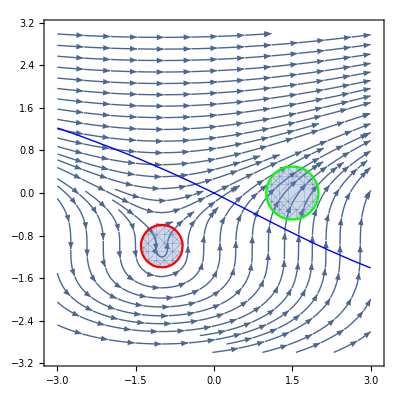

```mathematica
Show[
StreamPlot[vf,{x,-3,3},{y,-3,3}],
RegionPlot[init, {x,-3,3},{y,-3,3}, BoundaryStyle->Green],
RegionPlot[unsafe, {x,-3,3},{y,-3,3}, BoundaryStyle->Red],
ContourPlot[BCMclean==0, {x,-3,3},{y,-3,3}, ContourStyle->Directive[Thick, Blue]]
]
```

```mathematica
Minimize[{x+2 y,-5 x+y==7&&x+y≥26&&x≥0&&y≥0},{x,y}]
```

{293/6,{x→19/6,y→137/6}}

```mathematica
LinearProgramming[
{1,2},

{{-5,1},
{1,1}},

{{7,0},
{26,1}},

{{0,Infinity},
{0,Infinity}}
]
```

{19/6,137/6}

```mathematica
equations=First/@Select[BC, Head[#]==Equal&];
inequalities=First/@Select[BC, Head[#]==GreaterEqual&];
lpvars=(Variables/@(First/@BC))//Flatten//DeleteDuplicates//Sort;
```

```mathematica
lpvars
```

{COEFF1,COEFF10,COEFF2,COEFF3,COEFF4,COEFF5,COEFF6,COEFF7,COEFF8,COEFF9,λ10032,λ10033,λ10034,λ10035,λ10036,λ10037,λ10038,λ10039,λ10040,λ10041,λ10042,λ10043,λ10044,λ10045,λ10046,λ10047,λ10048,λ10049,λ10050,λ10051,λ10052,λ10053,λ10054,λ10055,λ10056,λ10057,λ10058,λ10059,λ10060,λ10061,λ10062,λ10063,λ10064,λ10065,λ10066,λ10067,λ10068,λ10069,λ10070,λ10071,λ10072,λ10073,λ10074,λ10075,λ10076,λ10077,λ10078,λ10079,λ10080,λ10081,λ10082,λ10083,λ10084,λ10085,λ10086,λ10087,λ10088,λ10089,λ10090,λ10091,λ10092,λ10093,λ10094,λ10095,λ10096,λ10097,λ10098,λ10099,λ10100,λ10101,λ10102,λ10103,λ10104,λ10105,λ10106,λ10107,λ10108,λ10109,λ10110,λ10111,λ10112,λ10113,λ10114,λ10115,λ10116,λ10117,λ10118,λ10119,λ10120,λ10121,λ10122}

```mathematica
inequalities
```

{λ2286,λ2287,λ2288,λ2289,λ2290,λ2291,λ2292,λ2293,λ2294,λ2295,λ2296,λ2297,λ2298,λ2299,λ2300,λ2301,λ2302,λ2303,λ2304,λ2305,λ2306,λ2307,λ2308,λ2309,λ2310,λ2311,λ2312,λ2313,λ2314,λ2315,λ2316,λ2317,λ2318,λ2319,λ2320,λ2321,λ2322,λ2323,λ2324,λ2325,λ2326,λ2327,λ2328,λ2329,λ2330,λ2331,λ2332,λ2333,λ2334,λ2335,λ2336,λ2337,λ2338,λ2339,λ2340,λ2341,λ2342,λ2343,λ2344,λ2345,λ2346,λ2347,λ2348,λ2349,λ2350,λ2351,λ2352,λ2353,λ2354,λ2355,λ2356,λ2357,λ2358,λ2359,λ2360,λ2361,λ2362,λ2363,λ2364,λ2365,λ2366,λ2367,λ2368,λ2369,λ2370,λ2371,λ2372,λ2373,λ2374,λ2375,λ2376,λ2377,λ2378,λ2379,λ2380,λ2381,λ2382,λ2383,λ2384,λ2385,λ2386,λ2387,λ2388,λ2389,λ2390,λ2391,λ2392,λ2393,λ2394,λ2395,λ2396,λ2397,λ2398,λ2399,λ2400,λ2401,λ2402,λ2403,λ2404,λ2405,λ2406,λ2407,λ2408,λ2409,λ2410,λ2411,λ2412,λ2413,λ2414,λ2415,λ2416,λ2417,λ2418,λ2419,λ2420,λ2421,λ2422,λ2423,λ2424,λ2425,λ2426,λ2427,λ2428,λ2429,λ2430,λ2431,λ2432,λ2433,λ2434,λ2435,λ2436,λ2437,λ2438,λ2439,λ2440,λ2441,λ2442,λ2443,λ2444,λ2445,λ2446,λ2447,λ2448,λ2449,λ2450,λ2451,λ2452,λ2453,λ2454,λ2455,λ2456,λ2457,λ2458,λ2459,λ2460,λ2461,λ2462,λ2463,λ2464,λ2465,λ2466,λ2467,λ2468,λ2469,λ2470,λ2471,λ2472,λ2473,λ2474,λ2475,λ2476,λ2477,λ2478,λ2479,λ2480,λ2481,λ2482,λ2483,λ2484,λ2485,λ2486,λ2487,λ2488,λ2489,λ2490,λ2491,λ2492}

```mathematica
Aeq=Map[Grad[#,lpvars]&,equations]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},68,{0,0,0,0,0,0,0,0,-2,-2,-4,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,170,-162,-27,0,-972,-243,-54,-9,0,-1215,-324,-81,-18,-3,0,243,486,81,729,162,27,972,243,54,9,1215,324,81,18,3}}
 |  |  |  |

```mathematica
MSet["aeq", Aeq]
```

```mathematica
ConstTerm[P_,vars_List]:=(Table[0,Length[vars]]/.CoefficientRules[P,vars])/.{a_List:>0}
```

```mathematica
beq=Map[-ConstTerm[#,lpvars]&, equations]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/100,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
MSet["beq", beq]
```

```mathematica
Aineq=Map[-Grad[#,lpvars]&,inequalities]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},205,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,140,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1}}
 |  |  |  |

```mathematica
MSet["aineq", Aineq]
```

```mathematica
bineq=Table[0, Length[inequalities]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
MSet["bineq",bineq]
```

```mathematica
const=Map[If[StringContainsQ[ToString[#], "λ"], 0,-Infinity]&,lpvars]
```

{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
objFn=#*0&/@lpvars
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
MSet["f", objFn]
```

```mathematica
MEvaluate["lpsl = linprog(f,aineq,bineq,aeq,beq)"]
```

Optimal solution found.


lpsl =

   -0.0000
   -0.0000
   -0.0001
   -0.0000
   -0.0002
   -0.0005
   -0.0015
   -0.0000
   -0.0015
   -0.0027
   -0.0065
   -0.0000
   -0.0119
         0
         0
   -0.0000
   -0.0000
   -0.0000
   -0.0000
   -0.0000
   -0.0000
         0
         0
         0
         0
         0
         0
         0
         0
         0
         0
         0
         0
         0
         0
         0
         0
         0
         0
         0
         0
         0
         0
         0
         0
    0.0000
         0
    0.0004
    0.0000
         0
         0
         0
    0.0000
    0.0000
    0.0013
         0
    0.0094
    0.0000
   -0.0000
   -0.0000
         0
    0.0000
         0
         0
    0.0000
    0.0002
         0
    0.0000
         0
         0
         0
    0.0060
         0
         0
    0.0000
         0
         0
         0
         0
         0
    0.0004
         0
    0.0000
    0.0000
         0
         0
    0.0000
         0
         0
         0
    0.0003
         0
    0.0000
    0.0018
         0
    0.0078
         0
    0.0000
         0
         0
         0
    0.0127
         0
    0.0000
         0
    0.0000
         0
         0
         0
         0
         0
    0.0004
    0.0054
         0
         0
    0.0004
         0
         0
         0
         0
   -0.0000
         0
         0
         0
    0.0000
         0
         0
         0
   -0.0000
    0.0017
         0
         0
         0
         0
         0
         0
         0
         0
         0
         0
         0
         0
         0
    0.0000
    0.0000
         0
         0
    0.0000
         0
    0.0000
         0
         0
         0
         0
   -0.0000
         0
         0
         0
    0.0000
         0
         0
         0
         0
         0
    0.0000
         0
         0
         0
         0
         0
         0
   -0.0000
    0.0000
         0
         0
         0
         0
         0
         0
         0
         0
         0
    0.0000
         0
         0
         0
    0.0000
         0
         0
         0
         0
         0
   -0.0000
   -0.0000
         0
         0
         0
         0
         0
    0.0000
         0
         0
         0
         0
         0
         0
         0
         0
    0.0000
         0
         0
         0
         0
   -0.0000
         0
         0
         0
         0
         0
         0
         0
         0
         0
   -0.0000
         0
         0
         0
         0

```mathematica
BC
```

{COEFF2-λ2138+λ2140==0,-1/100+COEFF3-(7 λ2137)/5-(7 λ2138)/5-λ2139+(3 λ2140)/5+(3 λ2141)/5==0,COEFF1-λ2137+λ2141==0,-COEFF2-λ2143+λ2145==0,-COEFF3+λ2142-λ2143/2-λ2144-λ2145/2-2 λ2146==0,-COEFF1-λ2142+λ2146==0,-2 COEFF1-λ2150-λ2154==0,-λ2147-λ2156==0,-λ2148+λ2153+λ2157-λ2159==0,-2 COEFF1-COEFF2+COEFF3-(49 λ2147)/25-(49 λ2148)/25-(7 λ2149)/5-(49 λ2150)/25-(7 λ2151)/5-λ2152-(7 λ2153)/10-λ2154/4-λ2155/2-4 λ2156-(14 λ2157)/5-2 λ2158-λ2159==0,COEFF1-COEFF2-(14 λ2147)/5-(7 λ2148)/5-λ2149-λ2153/2+4 λ2156+(7 λ2157)/5+λ2158+λ2159/2==0,-4 COEFF1+COEFF2-(7 λ2148)/5-(14 λ2150)/5-λ2151+(7 λ2153)/5+λ2154+λ2155-2 λ2157+2 λ2159==0,λ2137≥0,λ2138≥0,λ2139≥0,λ2140≥0,λ2141≥0,λ2142≥0,λ2143≥0,λ2144≥0,λ2145≥0,λ2146≥0,λ2147≥0,λ2148≥0,λ2149≥0,λ2150≥0,λ2151≥0,λ2152≥0,λ2153≥0,λ2154≥0,λ2155≥0,λ2156≥0,λ2157≥0,λ2158≥0,λ2159≥0}

```mathematica
LPres=LinearProgramming[
objFn,

Join[Aeq,Aineq],

Join[beq,bineq],

const
];
```

-(9493948827337263880625 COEFF1)/93143795436220270848277445088-(713156807451896631066375 COEFF10)/31047931812073423616092481696-(13890078517346651362125 COEFF11)/970247869127294488002890053-(2665471401119510789217875 COEFF12)/46571897718110135424138722544-(498011051261139202034875 COEFF13)/62095863624146847232184963392-(12147771182870019761922375 COEFF14)/31047931812073423616092481696-(961165509371310029548275 COEFF15)/31047931812073423616092481696-(5437060798591567265861775 COEFF16)/62095863624146847232184963392-(43406423609241413583953825 COEFF17)/31047931812073423616092481696-(1914817020865600546320075 COEFF18)/7761982953018355904023120424-(101396665435319518973940325 COEFF19)/15523965906036711808046240848-(25878839854478678109375 COEFF2)/124191727248293694464369926784-(603823357573317466060535775 COEFF20)/124191727248293694464369926784+(458022696816440971909216775 COEFF21)/124191727248293694464369926784-(29363049739370672939375 COEFF3)/23285948859055067712069361272-(149430786026890829375 COEFF4)/15523965906036711808046240848-(4630026172448883787375 COEFF6)/970247869127294488002890053-(53503099222036262388125 COEFF7)/124191727248293694464369926784-(710874935936814005028125 COEFF8)/46571897718110135424138722544+(117003906599402019269375 COEFF9)/31047931812073423616092481696+(4630026172448883787375 λ2317)/970247869127294488002890053+(31201022869484001814839903 λ2321)/7761982953018355904023120424+(9493948827337263880625 λ2322)/93143795436220270848277445088+(29363049739370672939375 λ2325)/23285948859055067712069361272+(1046301803054614852538375 λ2326)/93143795436220270848277445088+(1786893302592321793354475 λ2327)/46571897718110135424138722544+(188013176803588441309625 λ2329)/31047931812073423616092481696+(31977849709979583680875 λ2330)/15523965906036711808046240848+(9206184958330181822118125 λ2333)/62095863624146847232184963392+(1296824448469222857392255 λ2335)/1940495738254588976005780106+(5018789937039837975377332 λ2336)/970247869127294488002890053+(25878839854478678109375 λ2337)/124191727248293694464369926784+(149430786026890829375 λ2340)/15523965906036711808046240848+(7780588611199317635966375 λ2344)/62095863624146847232184963392+(9493948827337263880625 λ2347)/93143795436220270848277445088+(25878839854478678109375 λ2348)/124191727248293694464369926784+(623140028862272095225625 λ2349)/745150363489762166786219560704+(538946196798182245380625 λ2351)/31047931812073423616092481696+(9497218486483717926792125 λ2352)/186287590872440541696554890176+(149430786026890829375 λ2353)/15523965906036711808046240848+(3418699022213750583987375 λ2355)/62095863624146847232184963392+(43839973399254236695080325 λ2356)/186287590872440541696554890176+(1010076205632732756775875 λ2358)/31047931812073423616092481696+(220738751587779565308590925 λ2360)/124191727248293694464369926784+(4398792768708378913988851925 λ2361)/745150363489762166786219560704+(4630026172448883787375 λ2362)/970247869127294488002890053+(144507280885123182260925 λ2364)/3880991476509177952011560212+(13274082785295480556747025 λ2365)/23285948859055067712069361272+(132331870243985539221687725 λ2366)/23285948859055067712069361272+(29363049739370672939375 λ2369)/23285948859055067712069361272+(4630026172448883787375 λ2374)/1940495738254588976005780106+(21032202520359198559954625 λ2376)/62095863624146847232184963392+(4630026172448883787375 λ2393)/1940495738254588976005780106+(39660724254086978805625 λ2409)/2235451090469286500358658682112+(129309367957793051290625 λ2411)/1117725545234643250179329341056+(26666000566837905813125 λ2414)/15523965906036711808046240848+(22681600234437197531136125 λ2418)/6706353271407859501075976046336+(54995987101371067559309975 λ2423)/6706353271407859501075976046336+(9503937350533017946625 λ2436)/124191727248293694464369926784+(3775190872746176488716575 λ2446)/6706353271407859501075976046336+(52897792121064730003025 λ2452)/11642974429527533856034680636+(1009964491322678614384375 λ2460)/1117725545234643250179329341056+(393580356179613851875 λ2463)/7761982953018355904023120424+(28057749715195325308103875 λ2467)/6706353271407859501075976046336+(2123440826265434321559725 λ2472)/279431386308660812544832335264+(131410148055507344233625 λ2478)/2235451090469286500358658682112+(4238885542865754091305125 λ2489)/1117725545234643250179329341056

```mathematica
BCs=LPres.lpvars
```

-(9493948827337263880625 COEFF1)/93143795436220270848277445088-(713156807451896631066375 COEFF10)/31047931812073423616092481696-(13890078517346651362125 COEFF11)/970247869127294488002890053-(2665471401119510789217875 COEFF12)/46571897718110135424138722544-(498011051261139202034875 COEFF13)/62095863624146847232184963392-(12147771182870019761922375 COEFF14)/31047931812073423616092481696-(961165509371310029548275 COEFF15)/31047931812073423616092481696-(5437060798591567265861775 COEFF16)/62095863624146847232184963392-(43406423609241413583953825 COEFF17)/31047931812073423616092481696-(1914817020865600546320075 COEFF18)/7761982953018355904023120424-(101396665435319518973940325 COEFF19)/15523965906036711808046240848-(25878839854478678109375 COEFF2)/124191727248293694464369926784-(603823357573317466060535775 COEFF20)/124191727248293694464369926784+(458022696816440971909216775 COEFF21)/124191727248293694464369926784-(29363049739370672939375 COEFF3)/23285948859055067712069361272-(149430786026890829375 COEFF4)/15523965906036711808046240848-(4630026172448883787375 COEFF6)/970247869127294488002890053-(53503099222036262388125 COEFF7)/124191727248293694464369926784-(710874935936814005028125 COEFF8)/46571897718110135424138722544+(117003906599402019269375 COEFF9)/31047931812073423616092481696+(4630026172448883787375 λ2317)/970247869127294488002890053+(31201022869484001814839903 λ2321)/7761982953018355904023120424+(9493948827337263880625 λ2322)/93143795436220270848277445088+(29363049739370672939375 λ2325)/23285948859055067712069361272+(1046301803054614852538375 λ2326)/93143795436220270848277445088+(1786893302592321793354475 λ2327)/46571897718110135424138722544+(188013176803588441309625 λ2329)/31047931812073423616092481696+(31977849709979583680875 λ2330)/15523965906036711808046240848+(9206184958330181822118125 λ2333)/62095863624146847232184963392+(1296824448469222857392255 λ2335)/1940495738254588976005780106+(5018789937039837975377332 λ2336)/970247869127294488002890053+(25878839854478678109375 λ2337)/124191727248293694464369926784+(149430786026890829375 λ2340)/15523965906036711808046240848+(7780588611199317635966375 λ2344)/62095863624146847232184963392+(9493948827337263880625 λ2347)/93143795436220270848277445088+(25878839854478678109375 λ2348)/124191727248293694464369926784+(623140028862272095225625 λ2349)/745150363489762166786219560704+(538946196798182245380625 λ2351)/31047931812073423616092481696+(9497218486483717926792125 λ2352)/186287590872440541696554890176+(149430786026890829375 λ2353)/15523965906036711808046240848+(3418699022213750583987375 λ2355)/62095863624146847232184963392+(43839973399254236695080325 λ2356)/186287590872440541696554890176+(1010076205632732756775875 λ2358)/31047931812073423616092481696+(220738751587779565308590925 λ2360)/124191727248293694464369926784+(4398792768708378913988851925 λ2361)/745150363489762166786219560704+(4630026172448883787375 λ2362)/970247869127294488002890053+(144507280885123182260925 λ2364)/3880991476509177952011560212+(13274082785295480556747025 λ2365)/23285948859055067712069361272+(132331870243985539221687725 λ2366)/23285948859055067712069361272+(29363049739370672939375 λ2369)/23285948859055067712069361272+(4630026172448883787375 λ2374)/1940495738254588976005780106+(21032202520359198559954625 λ2376)/62095863624146847232184963392+(4630026172448883787375 λ2393)/1940495738254588976005780106+(39660724254086978805625 λ2409)/2235451090469286500358658682112+(129309367957793051290625 λ2411)/1117725545234643250179329341056+(26666000566837905813125 λ2414)/15523965906036711808046240848+(22681600234437197531136125 λ2418)/6706353271407859501075976046336+(54995987101371067559309975 λ2423)/6706353271407859501075976046336+(9503937350533017946625 λ2436)/124191727248293694464369926784+(3775190872746176488716575 λ2446)/6706353271407859501075976046336+(52897792121064730003025 λ2452)/11642974429527533856034680636+(1009964491322678614384375 λ2460)/1117725545234643250179329341056+(393580356179613851875 λ2463)/7761982953018355904023120424+(28057749715195325308103875 λ2467)/6706353271407859501075976046336+(2123440826265434321559725 λ2472)/279431386308660812544832335264+(131410148055507344233625 λ2478)/2235451090469286500358658682112+(4238885542865754091305125 λ2489)/1117725545234643250179329341056

```mathematica
Table[0,Length[{x,y,z}]]/.CoefficientRules[x^2+y^3-z-1345,{x,y,z}]
```

-1345

```mathematica
-ConstTerm[x-y+1,{x,y}]
```

-1